# A Computational Perspective on Sexual Reproduction

## Intro

I think sex is actually fundamental for the complexity we observe in biology. I think understanding it is critical to understanding biological evolution, as well as other adaptive processes. Further, in getting to the computational essence of sex, many phenomena that appear bizarre at first glance, like the ubiquity of the male-female system, hierarchy, and the different sex characteristics, become explainable.    

When I say sex, I mean the process of recombining genes as well as all the behaviors that developed around that, namely meiosis and the two-sex system, or what biologists call dioecy. But dioecy shmioecy, it is actually easy to explain these phenomena without getting weighed down by the intricate mechanisms of biology, as many biologists do. At its core, sex is about the exchange of bits, so to understand it we only need to carefully examine the world of simple programs. 

In Wolfram’s post on CAs in evolution, he came to the conclusion that sexual reproduction was not fundamental for understanding evolution. But I think this is wrong. Wolfram’s model for sex was to have a Cellular Automata and then basically split the two rule sets in half and combine them. The resulting program was then ran and the fitness was measured on the length for which the program runs. He noted that this process seemed to work fine, but concluded that it didn’t offer any fundamental new behavior. Because of this, he dismissed it as unimportant for understanding the high-level concepts in evolution. 

I think the fact that sex did not work in his model tells us something about an important difference between the CA model and how genes are actually set up. Namely, that there is more connectivity between rules in the CA than there are between genes in a cell. But it’s actually easy to set up a CA model where sex is obviously advantageous. So, we can set up “multi-gene” automata like so:

## V1

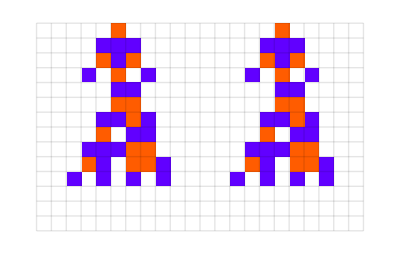

```mathematica
plotorg[initorgs[[1]]]
```

And this would be one organism’s genome:

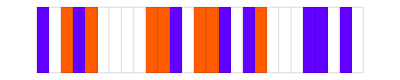
{-Graphics-,-Graphics-}

```mathematica
initorgs = {{diffsmemo[[48, 1]], diffsmemo[[48, 16]]}, {diffsmemo[[48, 2]], diffsmemo[[48,-3]]}};
initorgs = {{initrule,initrule}, {initrule, initrule}};
plotrule/@ initorgs[[1]]
```

And its fitness corresponds to the sum of the lengths of the two separate programs. Each of these automata have length 11, so the fitness of this organism would be 22.
To evolve, we choose a random “gene” from the automata and perform a random point mutation on that gene, like so:

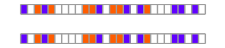
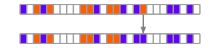

```mathematica
mutes = mutate[initorgs[[1]]];
Row[rulesmutationplot/@ Transpose[{initorgs[[1]], mutes}]]
```

Here is the corresponding phenotype change:

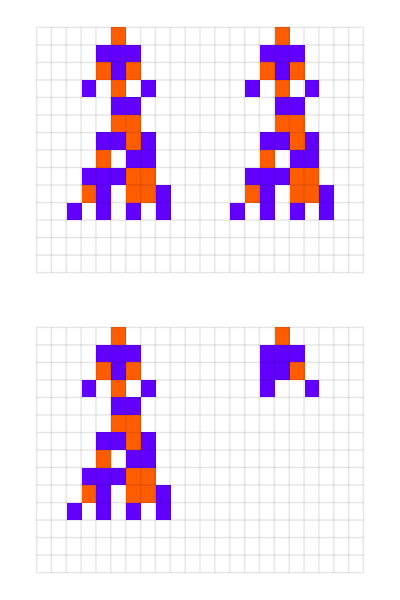

```mathematica
Column[plotorg/@ {initorgs[[1]], mutes}]
```

Just like before, we only accept organisms with higher or equal fitness. So the above case would be rejected because the automata on the right only has length 4, so the total fitness of the new organism is 15, which is less than the original 22. Note that if either rule goes to infinity, then the organism has fitness 0, like this case:

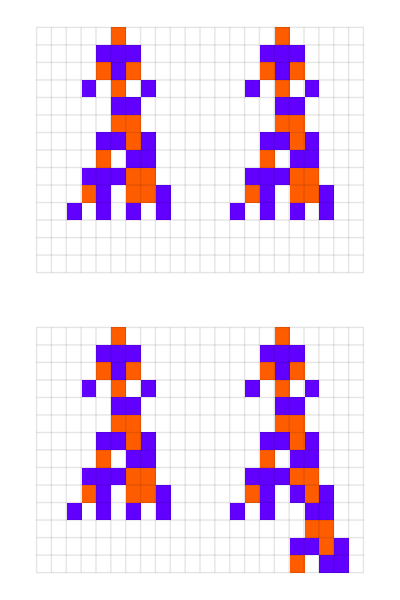

```mathematica
mutes2 = mutate[initorgs[[1]]];
Column[plotorg/@ {initorgs[[1]], mutes2}]
```

We repeat this process, here showing 11 steps in an evolution:

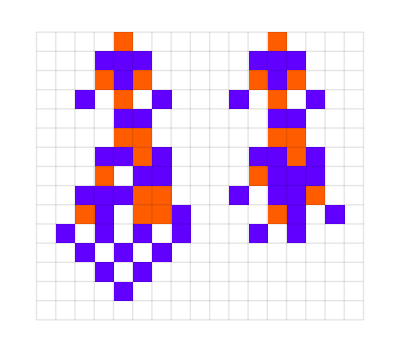
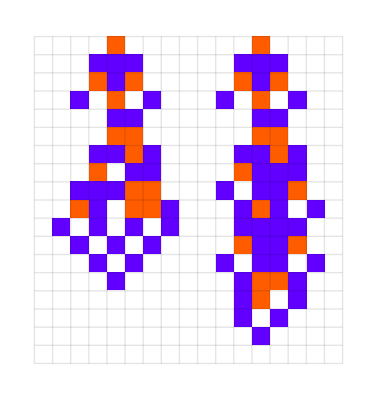
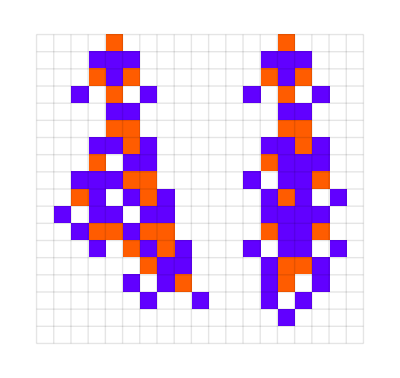
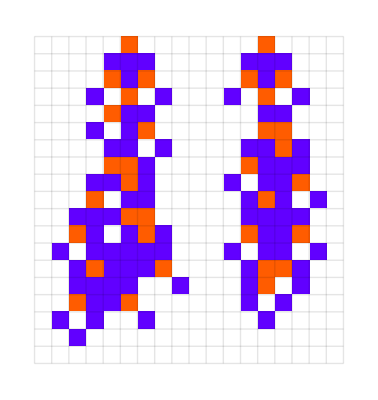
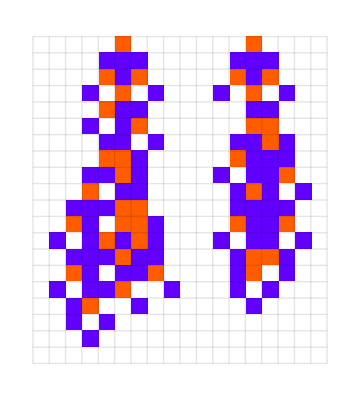
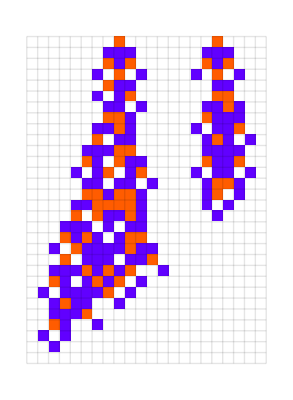
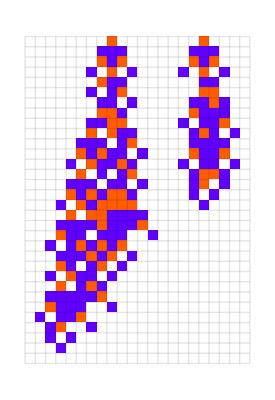
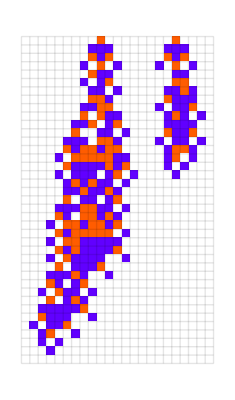

```mathematica
cut=200;
evo1=NestList[CompoundExpression[
ru=mutate[First[#]],
life=testlifetime[ru[[1]], cut] + testlifetime[ru[[2]], cut],
If[life>=Last[#],{ru,life},#]
]&,{initorgs[[1]],22},4000];
evo2=Rest[First/@SplitBy[evo1,Last]];
plotorg/@ evo2[[All, 1]]
```

And here is the evolution of the summed lifetime:

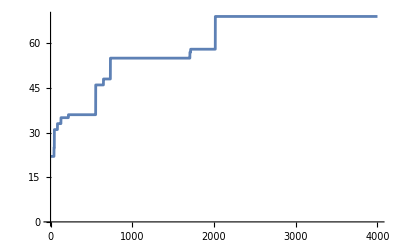

```mathematica
ListLinePlot[evo1[[All, 2]]]
```

Now we simply define a population as two of these double-automata like so

```mathematica
plotorg/@ initorgs
```

{-Graphics-,-Graphics-}

And here is how our population evolve:

```mathematica
evosnew = Table[NestList[CompoundExpression[
ru=mutate[First[#]],
life=testlifetime[ru[[1]], cut] + testlifetime[ru[[2]], cut],
If[life>=Last[#],{ru,life},#]
]&,{initorgs[[1]],22},4000], 5, 2];
```

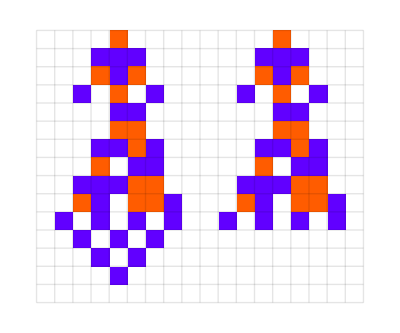
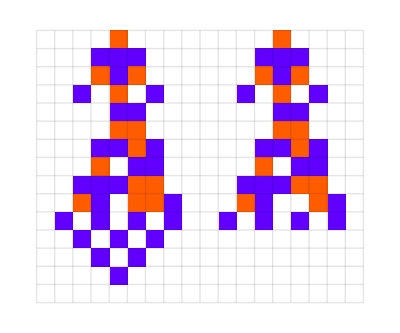
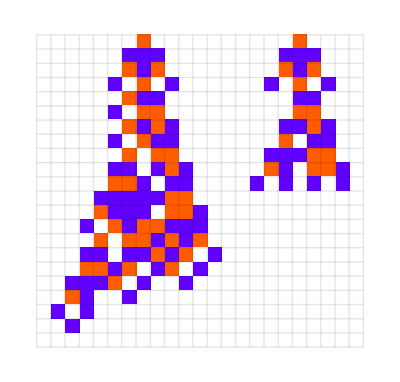
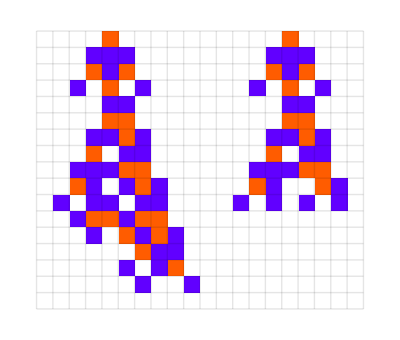
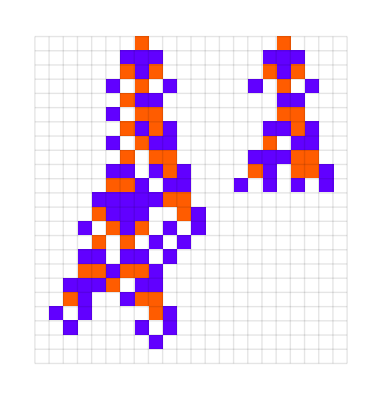
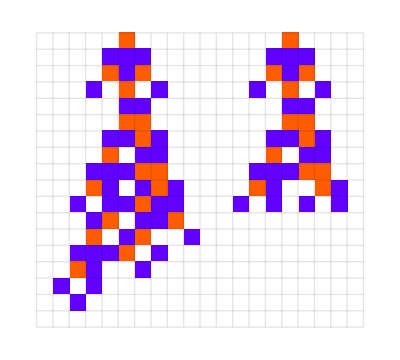
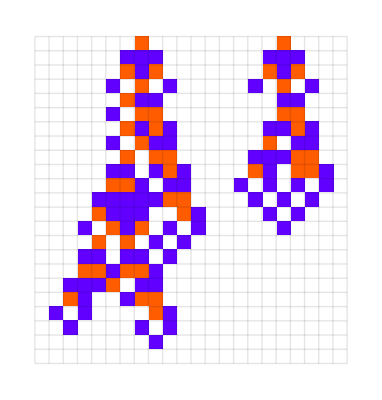
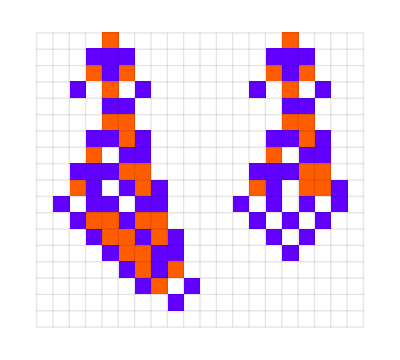

```mathematica
evos2=Map[Rest[First/@SplitBy[#,Last]]&,evosnew, {2}];
tevos = Transpose[{#[[1, ;;Min[Length/@#] ]],#[[2,;;Min[Length/@#] ]]}]&/@ evos2;
Column[Map[plotorg[#[[1]]]&, tevos[[5]], {2}]]
```

And here is the the growth of lifetimes:

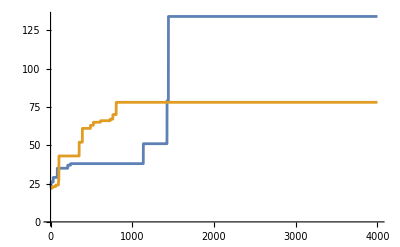

```mathematica
ListLinePlot[{evos[[1, All, 2]], evos[[2, All, 2]]}]
```

Doing 5 runs here are our different evolution paths:

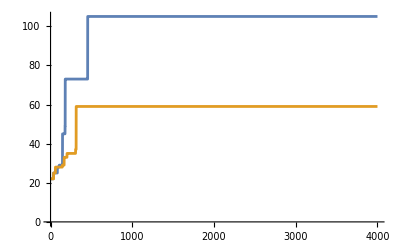
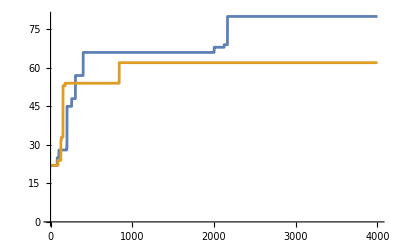
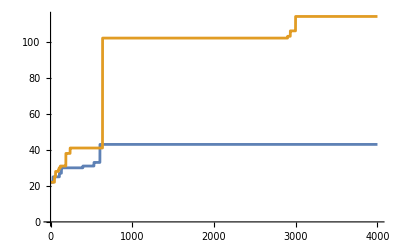
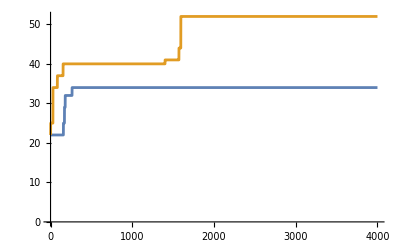
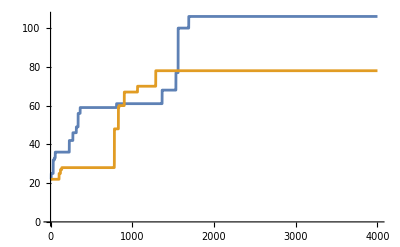

```mathematica
ListLinePlot[{#[[1, All, 2]], #[[2, All, 2]]}, PlotHighlighting->None]&/@ evosnew
```

So this would be the analog to asexual reproduction. One thing to note is sometimes one organism jumps way ahead of another organism. You may see where I’m going with this, but now let’s see the equivalent sexual reproduction population. All we’ll do, is if one organism discovers a longer automata, they’ll share it with the other organism. If this would increase the fitness of the other organism, in either gene, they will replace the less fit gene with the new rule.

```mathematica
initorgs[[1]]
```

{{5586032021307,3,1},{5586032021307,3,1}}

```mathematica
io =Map[ {#, testlifetime[#, 200]}&, initorgs, {2}]
```

{{{{5586032021307,3,1},11},{{5586032021307,3,1},11}},{{{5586032021307,3,1},11},{{5586032021307,3,1},11}}}

```mathematica
io = Transpose[{initorgs, {22, 22}}]
```

{{{{5586032021307,3,1},{5586032021307,3,1}},22},{{{5586032021307,3,1},{5586032021307,3,1}},22}}

```mathematica
io[[All, 1]]
```

{{{5586032021307,3,1},{5586032021307,3,1}},{{5586032021307,3,1},{5586032021307,3,1}}}

```mathematica
rus=mutate/@io[[All, 1]]
```

{{{5586032021307,3,1},{5586032021280,3,1}},{{5586031667013,3,1},{5586032021307,3,1}}}

```mathematica
lives=Total[testlifetime/@ #]&/@ rus
```

{13,-∞}

```mathematica
Transpose[{rus, lives}]
```

{{{{5586032021307,3,1},{5586032021253,3,1}},13},{{{5586032552748,3,1},{5586032021307,3,1}},-∞}}

```mathematica
io
```

{{{{5586032021307,3,1},11},{{5586032021307,3,1},11}},{{{5586032021307,3,1},11},{{5586032021307,3,1},11}}}

```mathematica
kept = MapThread[If[#1[[-1]]>=#2[[-1]],#1, #2]&, {Transpose[{rus, lives}], io}]
```

{{{{5586032021307,3,1},{5586032021307,3,1}},22},{{{5586032021307,3,1},{5586032021307,3,1}},22}}

```mathematica
max = MaximalBy[kept[[1]], io[[2]]&]

min = MinimalBy[kept[[2]], io[[2]]&]
```

{{{5586032021307,3,1},{5586032021307,3,1}},22}

{{{5586032021307,3,1},{5586032021307,3,1}},22}

```mathematica
kept[[1, 1]]
```

{{5586032021307,3,1},{5586032021307,3,1}}

```mathematica
kept[[1, 1]]
```

{{5586032021307,3,1},{5586032021307,3,1}}

```mathematica
ReplaceAll[kept[[2]], min->max]
```

{{{5586032021307,3,1},{5586032021307,3,1}},22}

```mathematica
out= {kept[[1]],ReplaceAll[kept[[2]], min->max]}
```

{{{{5586032021307,3,1},{5586032021307,3,1}},22},{{{5586032021307,3,1},{5586032021307,3,1}},22}}

```mathematica
out[[3]]
```

Part::partw: Part 3 of {{{{5586032021307,3,1},{5586032021307,3,1}},22},{{{5586032021307,3,1},{5586032021307,3,1}},22}} does not exist.

{{{{5586032021307,3,1},{5586032021307,3,1}},22},{{{5586032021307,3,1},{5586032021307,3,1}},22}}⟦3⟧

```mathematica
es= NestList[CompoundExpression[
rus=mutate/@#[[All, 1]],
lives=Total[testlifetime/@ #]&/@ rus,
kept = MapThread[If[#1[[-1]]>=#2[[-1]],#1, #2]&, {Transpose[{rus, lives}], #}],
max = MaximalBy[kept[[1, 1]], testlifetime[#, cut]&],
min = MinimalBy[kept[[2, 1]], testlifetime[#, cut]&],
{kept[[1]],ReplaceAll[kept[[2]], min->max]}
]&,Transpose[{initorgs, {22, 22}}], 10];
```

```mathematica
Table[If[ {i,1, 2}, {j,1,2}]
```

{{{1,1},{1,2}},{{2,1},{2,2}}}

```mathematica
rus
```

{{{5554650963885,3,1},{5561625120990,3,1}},{{5844054126030,3,1}}}

```mathematica
rus[[1, 1]]
```

{5586032021307,3,1}

```mathematica
io[[{1, 1}]]
```

{{{{5586032021307,3,1},{5586032021307,3,1}},22},{{{5586032021307,3,1},{5586032021307,3,1}},22}}

```mathematica
io[[2,1, 2]]
```

{5586032021307,3,1}

```mathematica
evo[orgs_]:= Block[{rus, lives, kept, max, min},
ors = orgs[[All,  1]];
ols = orgs[[All, 2]];
nrs=muorg/@ors;
nls=Map[testlifetime, rus, {2}];

Table[If[ lives[[i, j]]>=orgs[[{i,1, 2}, {j,1,2}]
kept = MapThread[If[#1[[-1]]>=#2[[-1]],#1, #2]&, {Transpose[{rus, lives}], orgs}];
max = PositionLargest[kept[[1, 1]], 1,testlifetime[#, cut]&][[1]];
min = PositionSmallest[kept[[2, 1]],1, testlifetime[#, cut]&][[1]];
{kept[[1]],ReplaceAll[kept[[2]], min->max]}
]
```

```mathematica
evosex[{org1_, org2_}]:=Block[{},

new = muorg/@{org1, org2};

]
```

```mathematica
PositionLa
```

```mathematica
es = NestList[evo,  Transpose[{initorgs, {22, 22}}], 3]
```

{{{{{5586032021307,3,1},{5586032021307,3,1}},22},{{{5586032021307,3,1},{5586032021307,3,1}},22}},{{{{5586032021307,3,1},{5586032021307,3,1}},22},{{{5586032021307,3,1},{5586032021307,3,1}},22}},{{{{5586032021307,3,1},{5586032021307,3,1}},22},{{{5586032021307,3,1},{5586032021307,3,1}},22}},{{{{5586032021307,3,1},{5586032021307,3,1}},22},{{{5586032021307,3,1},{5586032021307,3,1}},22}}}

```mathematica
evo[{{{{5554650961698,3,1},{5586161161470,3,1}},22},{{{5554650961698,3,1},{5586161161470,3,1}},22}}]
```

{{{{5554650961698,3,1},{5593134730272,3,1}},25},{{{5593134730272,3,1}},22}}

```mathematica
es[[3, 1]]
```

{{{5586032021307,3,1},{5554650961698,3,1}},22}

```mathematica
es[[4, 1]]
```

{{{5586032021307,3,1},{5561624530500,3,1}},25}

```mathematica
es[[3, All, 1]]
```

{{{5586032021307,3,1},{5554650961698,3,1}},{{5586032021307,3,1},{5554650961698,3,1}}}

```mathematica
es[[4, All, 1]]
```

{{{5586032021307,3,1},{5561624530500,3,1}},{{5561624530500,3,1}}}

## V2

```mathematica
murules[{initrule}]
```

{{5586031844160,3,1}}

```mathematica
org = {{{5586032021307,3,1},11},{{5586032021307,3,1},11}}
```

{{{5586032021307,3,1},11},{{5586032021307,3,1},11}}

### Asexual Population

So imagine instead of evolving one organism we simply evolve two simultaneously like so:

```mathematica
cut=200;
evo1=NestList[CompoundExpression[
rus=murules[#[[All, 1]]],
lives =testlifetime[#, cut] &/@ rus,
kept = MapThread[If[#1[[-1]]>=#2[[-1]],#1, #2]&, {Transpose[{rus, lives}], #}]]&,
org,10];
evo2=Rest[First/@SplitBy[evo1,{#[[1, -1]], #[[2, -1]]}&]];
plotorg/@ evo2
```

{-Graphics-}

```mathematica
org
```

{{{5586032021307,3,1},11},{{5586032021307,3,1},11}}

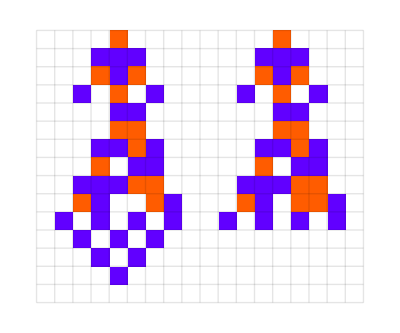
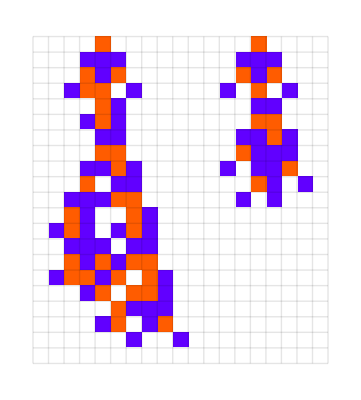
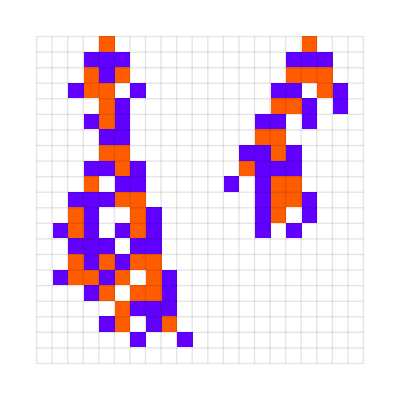
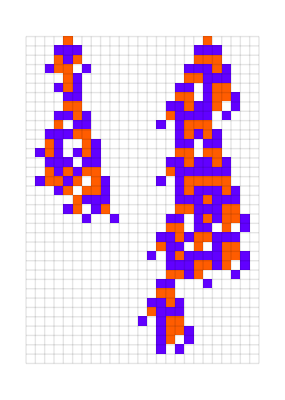
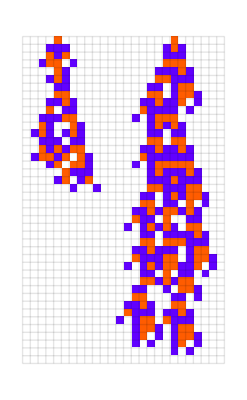
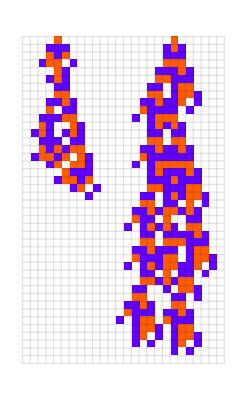

```mathematica
cut=200;
evo1=NestList[CompoundExpression[
new=muorg[#],
(*Echo[new],*)
kept = Table[ If[new[[i, 2]]>=#[[i , 2]], new[[i]], #[[i]]], {i, 1, 2}]]&,
org,1000];
evo2=Rest[First/@SplitBy[evo1,{#[[1, -1]], #[[2, -1]]}&]];
plotorg/@ evo2
```

```mathematica
.
```

```mathematica
rus
```

{{5586032021307,3,1},{5586032021301,3,1}}

```mathematica
init  = pop[[All, 1]]
```

{{{5586032021307,3,1},11},{{5586032021307,3,1},11}}

```mathematica
cut=200;
evo1=NestList[CompoundExpression[
new=muorg[#],
kept = MapThread[If[#1[[-1]]>=#2[[-1]],#1, #2]&, {new, #}]]&,
init,20];
evo2=Rest[First/@SplitBy[evo1,{#[[1, -1]], #[[2, -1]]}&]];
plotorg/@ evo2[[All,All, 1]]
```

CellularAutomaton::rsize: The specified rule number 5593007188806 is greater than the largest possible rule number (255).

CellularAutomaton::kspec: Since position 1 of rule specification {200,All} is not a function or rule list, position 2 (if present) must be of the form k, {k, 1}, or {k, wts} where k is a machine integer > 1 and wts is a non-empty array of non-negative machine integers.

CellularAutomaton::rsize: The specified rule number 5586030426984 is greater than the largest possible rule number (255).

CellularAutomaton::kspec: Since position 1 of rule specification {200,All} is not a function or rule list, position 2 (if present) must be of the form k, {k, 1}, or {k, wts} where k is a machine integer > 1 and wts is a non-empty array of non-negative machine integers.

CellularAutomaton::rsize: The specified rule number 5593007188806 is greater than the largest possible rule number (255).

General::stop: Further output of CellularAutomaton::rsize will be suppressed during this calculation.

ArrayPad::arr: First argument 5593007188806 to ArrayPad should be an array.

ArrayPad::arr: First argument 12 to ArrayPad should be an array.

ArrayPad::arr: First argument 5586030426984 to ArrayPad should be an array.

General::stop: Further output of ArrayPad::arr will be suppressed during this calculation.

MapThread::mptd: Object CellularAutomaton[5593007188806,{0,{1},0,0},12] at position {2, 1} in MapThread[Join[#1,#2]&,{CellularAutomaton[5593007188806,{0,{1},0,0},12],CellularAutomaton[5586030426984,{0,{1},0,0},12]}] has only 0 of required 1 dimensions.

ArrayPlot::mat: Argument MapThread[Join[#1,#2]&,{CellularAutomaton[5593007188806,{0,{1},0,0},12],CellularAutomaton[5586030426984,{0,{1},0,0},12]}] at position 1 is not a list of lists.

CellularAutomaton::kspec: Since position 1 of rule specification {200,All} is not a function or rule list, position 2 (if present) must be of the form k, {k, 1}, or {k, wts} where k is a machine integer > 1 and wts is a non-empty array of non-negative machine integers.

General::stop: Further output of CellularAutomaton::kspec will be suppressed during this calculation.

MapThread::mptd: Object CellularAutomaton[5594169450273,{0,{1},0,0},12] at position {2, 1} in MapThread[Join[#1,#2]&,{CellularAutomaton[5594169450273,{0,{1},0,0},12],CellularAutomaton[5585901286821,{0,{1},0,0},12]}] has only 0 of required 1 dimensions.

ArrayPlot::mat: Argument MapThread[Join[#1,#2]&,{CellularAutomaton[5594169450273,{0,{1},0,0},12],CellularAutomaton[5585901286821,{0,{1},0,0},12]}] at position 1 is not a list of lists.

{ArrayPlot[MapThread[Join[#1,#2]&,{CellularAutomaton[5593007188806,{0,{1},0,0},12],CellularAutomaton[5586030426984,{0,{1},0,0},12]}],ColorRules→{0→GrayLevel[1],1→Hue[0.06, 1, 1],2→Hue[0.73, 1, 1],3→Hue[0.14, 0.81, 0.99]},Mesh→True,MeshStyle→Opacity[0.1],ImageSize→Automatic],ArrayPlot[MapThread[Join[#1,#2]&,{CellularAutomaton[5594169450273,{0,{1},0,0},12],CellularAutomaton[5585901286821,{0,{1},0,0},12]}],ColorRules→{0→GrayLevel[1],1→Hue[0.06, 1, 1],2→Hue[0.73, 1, 1],3→Hue[0.14, 0.81, 0.99]},Mesh→True,MeshStyle→Opacity[0.1],ImageSize→Automatic]}

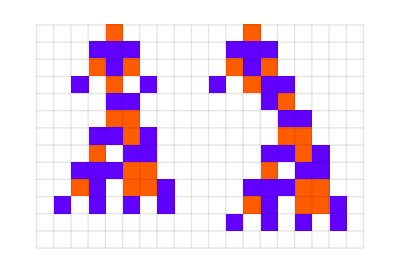
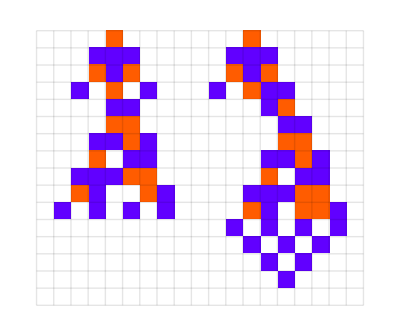
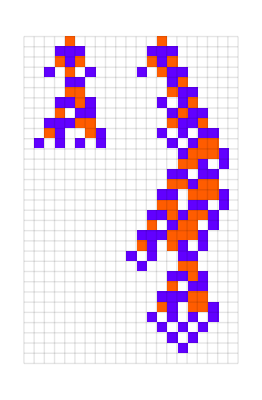
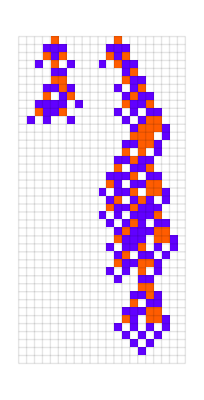
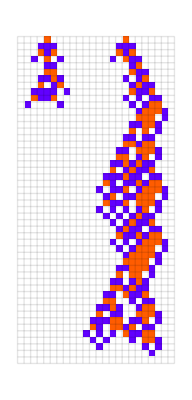
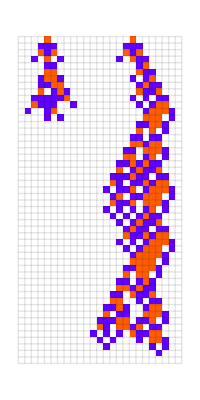
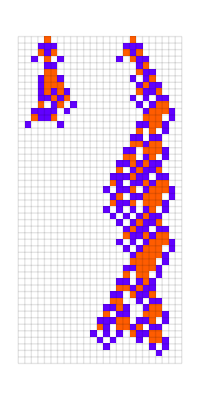
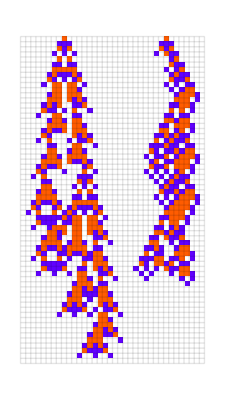

```mathematica
e1 = evosmemo2[[-1, 10]];
e2=Rest[First/@SplitBy[e1,{#[[1, -1]], #[[2, -1]]}&]];
plotorg/@ e2[[All, All, 1]]
```

And here is the growth of lifetimes:

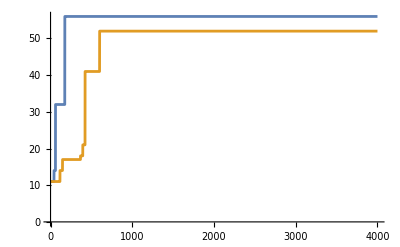

```mathematica
ListLinePlot[{e1[[All, 1, 2]], e1[[All, 2, 2]]}, PlotRange->All]
```

And with 10 runs

```mathematica
cut=200;
nevos=Table[NestList[CompoundExpression[
rus=muboth[#[[All, 1]]],
lives =testlifetime[#, cut] &/@ rus,
kept = MapThread[If[#1[[-1]]>=#2[[-1]],#1, #2]&, {Transpose[{rus, lives}], #}]]&,
Transpose[{initorgs[[1]],{11, 11}}],4000], 10];
```

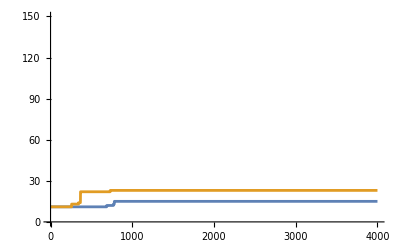
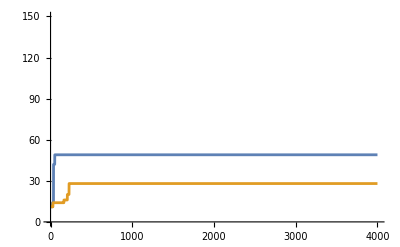
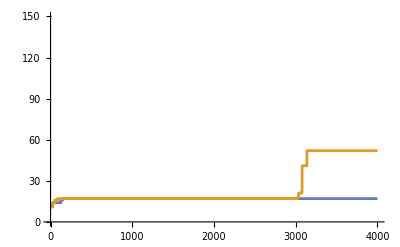
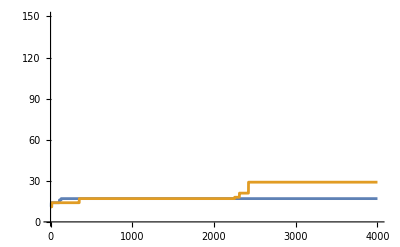
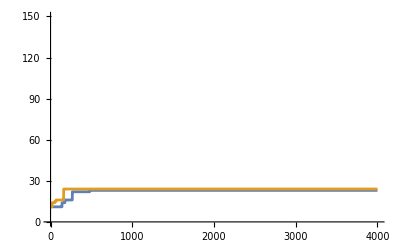
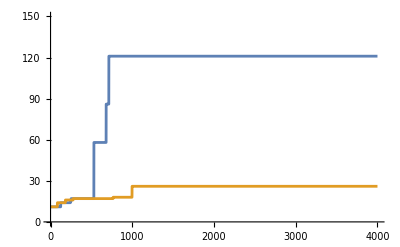
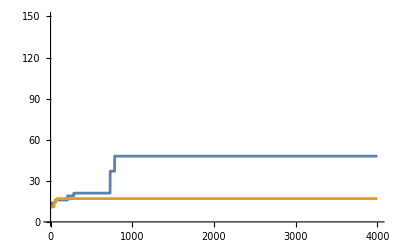
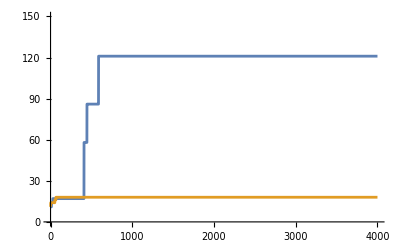

```mathematica
ListLinePlot[{#[[All, 1, 2]], #[[All, 2, 2]]}, PlotHighlighting->None, PlotRange->150]&/@ evosmemo2[[-1]]
```

So this would be the analog to complete asexual reproduction. One thing to note is sometimes one organism jumps way ahead of another organism. Let’s see what happens if we add some gene exchange. if a mutation is found that is more fit. Then that organism will look at the

### Sexual Population

```mathematica
SeedRandom[]
CompoundExpression[
rus=mupop[#[[All, 1]]],
oldlife = #[[1, 2]],
locdiffs = MapThread[locdiff[#1, #2]&, {rus, #[[All, 1]]}],
lives =testlifetime[#, cut] &/@ rus,
Echo[lives];
lar = If[AnyTrue[lives, #> oldlife&],  PositionLargest[lives, 1][[1]], {}],
If[lar != {},
start = If[locdiffs[[lar[[1]]]]<=14, 1,14];
gene = slice[rus[[lar[[1]]]], {start, start+13}];
Echo[Delete[#[[All, 1]], lar[[1]]]];
ins = insert[#, gene, start]&/@ Delete[#[[All, 1]], lar[[1]]];
Echo[ins];
Echo[rus = toru/@ ins]
],
kept = MapThread[If[#1[[-1]]>=#2[[-1]],#1, #2]&, {Transpose[{rus, lives}], #}]
]&[{{{5586032021307,3,1},11},{{5586032021307,3,1},11}}]
```

```mathematica
cut=200;
esex=NestList[CompoundExpression[
rus=mupop[#[[All, 1]]],
oldlife = #[[1, 2]],
locdiffs = MapThread[locdiff[#1, #2]&, {rus, #[[All, 1]]}],
lives =testlifetime[#, cut] &/@ rus,
lar = If[AnyTrue[lives, #> oldlife&],  PositionLargest[lives, 1][[1]], {}],
If[lar != {},
start = If[locdiffs[[lar[[1]]]]<=14, 1,14];
gene = slice[rus[[lar[[1]]]], {start, start+13}];
ins = toru/@(insert[#, gene, start]&)/@ Delete[#[[All, 1]], lar[[1]]];
(*Echo[{1, plot[rus[[lar[[1]]]], "nsteps"->20]}];*)
(*Echo[{1, plotrule[rus[[lar[[1]]]]]}];*)
(*Echo[{2, plot[#,"nsteps"->20]&/@ ins}];*)
(*Echo[{2, plotrule/@ ins}];*)
rus = Insert[ins, rus[[lar[[1]]]], lar[[1]]];
(*Echo[rus];*)
(*Echo[{1, plot[#, "nsteps"->20]&/@ rus}];*)
rus
],
kept = MapThread[If[#1[[-1]]>=#2[[-1]],#1, #2]&, {Transpose[{rus, lives}], #}]
]&,
Transpose[{initorgs[[1]],{11, 11}}],2000];
```

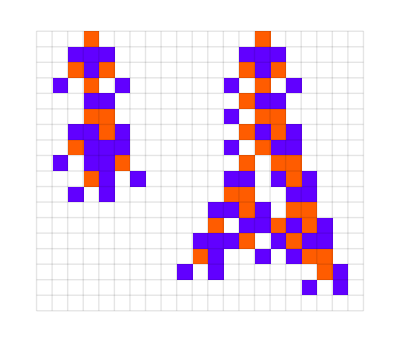
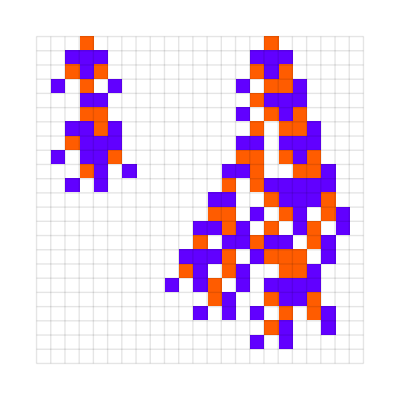
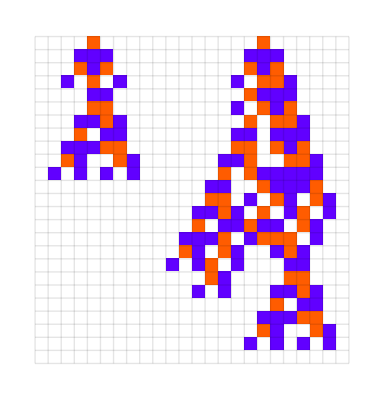
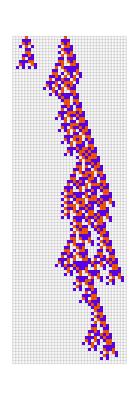
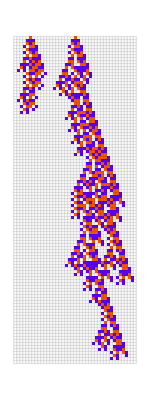
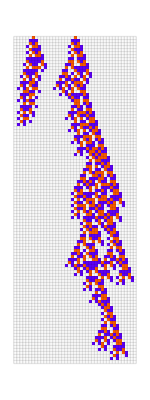

```mathematica
esex2=Rest[First/@SplitBy[esex,{#[[1, -1]], #[[2, -1]]}&]];
plotorg/@ esex2[[All,All, 1]]
```

```mathematica
slice[rule_, {start_, end_}]:= Block[{digits},
IntegerDigits[rule[[1]], rule[[2]], 27][[start;;end]]
]
```

```mathematica
ClearAll@insert
```

```mathematica
insert[rule_, vals_, loc_]:= Block[{digits, left, new, right},
digits = IntegerDigits[rule[[1]], rule[[2]], 27];
left = If[loc == 1, {}, digits[[;;loc-1]]];
right = If[loc == Length[vals], {}, digits[[loc+Length[vals];;]]];
Join[left, vals, right]
]
```

```mathematica
start
```

1

```mathematica
toru[digs_, base_:3, r_:1]:= {FromDigits[digs, base], base, r}
```

```mathematica
locdiff[rule1_, rule2_]:= Block[{},
digs = Transpose[IntegerDigits[#[[1]], #[[2]], 27]&/@ {rule1, rule2}];
FirstPosition[digs,_List?(#[[1]] != #[[2]]&)][[1]]
]
```

```mathematica
mu = randomrulemutation[initrule]
```

{5585902881144,3,1}

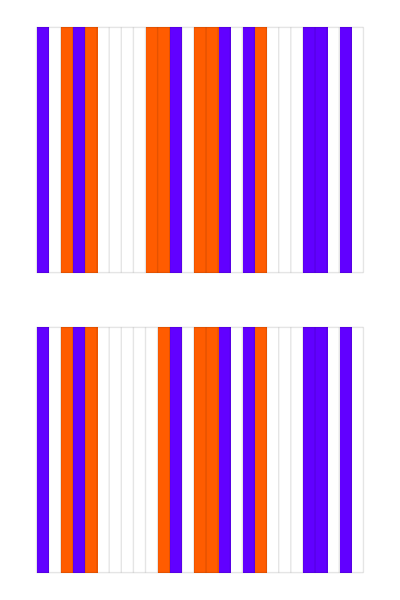

```mathematica
Column[plotrule/@ {initrule, mu}]
```

```mathematica
digs
```

{{2,2},{0,0},{1,1},{2,2},{1,1},{0,0},{0,0},{0,0},{0,0},{1,0},{1,1},{2,2},{0,0},{1,1},{1,1},{2,2},{0,0},{2,2},{1,1},{0,0},{0,0},{0,0},{2,2},{2,2},{0,0},{2,2},{0,0}}

```mathematica
locdiff[initrule, mu]
```

10

```mathematica
insert[initrule, slice[initrule, {10, 10}], 10]
```

{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0}

### Sexual Population V2

```mathematica
testlifetime[r =randomrulemutation[initrule]]
```

11

```mathematica
idxs = Reap[rs = Table[murand[initrule], 20]]
```

{{{{5589518805708,3,1},{5593005590109,3,1}},{{5586032014746,3,1},{5586032027868,3,1}},{{5585902881144,3,1},{5586161161470,3,1}},{{5586032021145,3,1},{5586032021226,3,1}},{{5587194282774,3,1},{5588356544241,3,1}},{{5586031667013,3,1},{5586031844160,3,1}},{{502300364649,3,1},{3044166192978,3,1}},{{5586032021253,3,1},{5586032021280,3,1}},{{5586032021253,3,1},{5586032021280,3,1}},{{5586031981941,3,1},{5586032001624,3,1}},{{5586030426984,3,1},{5586033615630,3,1}},{{5586419441796,3,1},{5586806862285,3,1}},{{5586030426984,3,1},{5586033615630,3,1}},{{5587194282774,3,1},{5588356544241,3,1}},{{5586031667013,3,1},{5586031844160,3,1}},{{5586032021316,3,1},{5586032021325,3,1}},{{5586419441796,3,1},{5586806862285,3,1}},{{5585988974586,3,1},{5586075068028,3,1}},{{5586032023494,3,1},{5586032025681,3,1}},{{5586031667013,3,1},{5586031844160,3,1}}},{{7,19,10,23,8,16,1,24,24,18,14,9,14,8,16,25,9,11,20,16}}}

```mathematica
ams = Flatten[getmutation[initrule, #]&/@ Range[26], 1]
```

{{502300364649,3,1},{3044166192978,3,1},{6433320630750,3,1},{7280609240193,3,1},{5303602484826,3,1},{5868461557788,3,1},{5397745663653,3,1},{5491888842480,3,1},{5554650961698,3,1},{5617413080916,3,1},{5596492374510,3,1},{5606952727713,3,1},{5589518805708,3,1},{5593005590109,3,1},{5587194282774,3,1},{5588356544241,3,1},{5586419441796,3,1},{5586806862285,3,1},{5585902881144,3,1},{5586161161470,3,1},{5585988974586,3,1},{5586075068028,3,1},{5586003323493,3,1},{5586017672400,3,1},{5586036804276,3,1},{5586041587245,3,1},{5586030426984,3,1},{5586033615630,3,1},{5586031489866,3,1},{5586032552748,3,1},{5586031667013,3,1},{5586031844160,3,1},{5586032080356,3,1},{5586032139405,3,1},{5586031981941,3,1},{5586032001624,3,1},{5586032014746,3,1},{5586032027868,3,1},{5586032023494,3,1},{5586032025681,3,1},{5586032022036,3,1},{5586032022765,3,1},{5586032021550,3,1},{5586032021793,3,1},{5586032021145,3,1},{5586032021226,3,1},{5586032021253,3,1},{5586032021280,3,1},{5586032021316,3,1},{5586032021325,3,1},{5586032021301,3,1},{5586032021304,3,1}}

```mathematica
ns = Join[{initrule}, Select[ams, testlifetime[#]>= 11&]]
```

{{5586032021307,3,1},{5554650961698,3,1},{5593005590109,3,1},{5585902881144,3,1},{5586161161470,3,1},{5586030426984,3,1},{5586033615630,3,1},{5586032080356,3,1},{5586032139405,3,1},{5586032023494,3,1},{5586032025681,3,1}}

```mathematica
testlifetime/@ ns
```

{11,11,14,11,11,11,11,11,11,11,11}

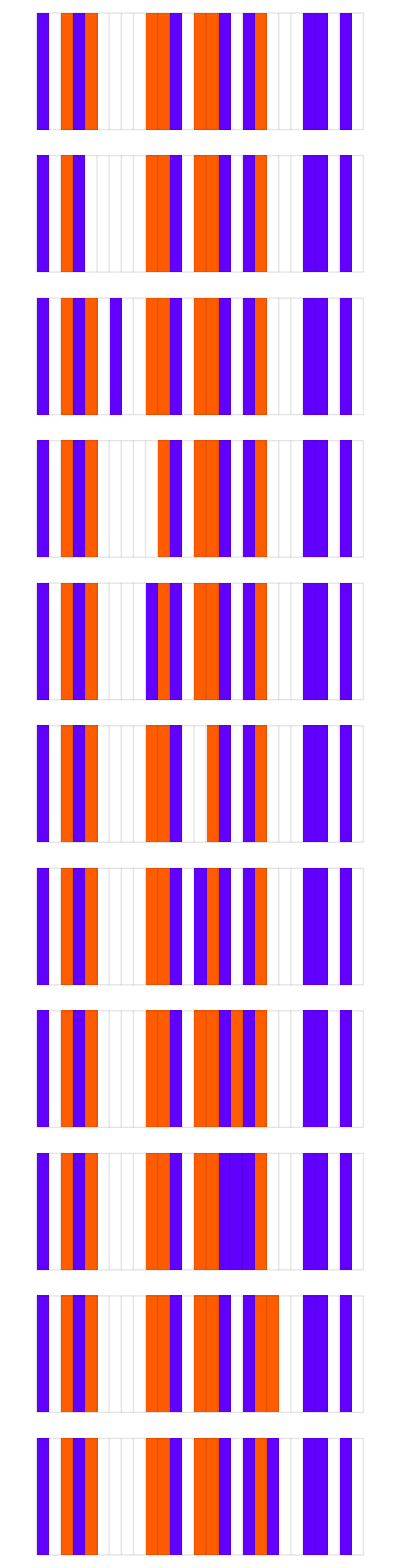

```mathematica
Column[plotrule/@Join[{initrule}, Select[ams, testlifetime[#]>= 11&]]]
```

```mathematica
lts = testlifetime/@ ams
```

{-∞,-∞,-∞,-∞,4,5,-∞,-∞,11,-∞,5,10,-∞,14,-∞,-∞,-∞,-∞,11,11,4,4,-∞,-∞,-∞,-∞,11,11,-∞,-∞,5,6,11,11,-∞,-∞,4,4,11,11,-∞,-∞,-∞,-∞,8,-∞,2,-∞,-∞,-∞,-∞,-∞}

```mathematica
idxs = Position[lts, _Integer?(# == 11&)]
```

{{9},{19},{20},{27},{28},{33},{34},{39},{40}}

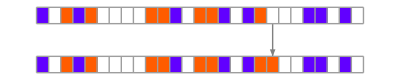

```mathematica
rulesmutationplot[{initrule, r}]
```

```mathematica
r2 = {5586032023494,3,1};
```

```mathematica
r1 = {5593005590109,3,1};
```

```mathematica
r3 = toru[insert[r1, slice[r2,{14, 27}], 14]]
```

{5593005592296,3,1}

```mathematica
ns = getneutral[initrule]
```

{{5554650961698,3,1},{5585902881144,3,1},{5586161161470,3,1},{5586030426984,3,1},{5586033615630,3,1},{5586032080356,3,1},{5586032139405,3,1},{5586032023494,3,1},{5586032025681,3,1}}

```mathematica
combine[r1_, r2_]:=Block[{ds = todigs/@ {r1, r2}},

toru[insert[r1, slice[r2,{14, 27}], 14]]
```

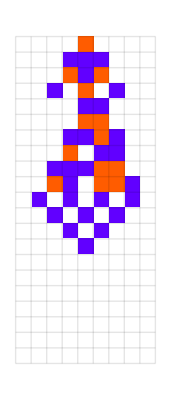

```mathematica
plot[r3, "nsteps"-> 20]
```

```mathematica
testlifetime/@getallmutations@r3
```

{-∞,-∞,-∞,-∞,5,5,-∞,-∞,14,-∞,6,13,11,-∞,-∞,-∞,-∞,-∞,14,14,4,6,-∞,-∞,-∞,-∞,14,14,-∞,-∞,5,-∞,14,14,-∞,-∞,-∞,4,14,14,-∞,-∞,-∞,-∞,8,-∞,3,-∞,-∞,-∞,-∞,-∞,-∞,-∞}

```mathematica
Length[%]
```

27

```mathematica
diffsmemo[[47, 9]]
```

{7280738380356,3,1}

```mathematica
ir2 =diffsmemo[[47, 9]];
```

And its fitness corresponds to the sum of the lengths of the two separate programs.  Each organism evolves separately by mutation, but when an organism finds a more fit program, it shares the new ruleset with the other organisms. The other organisms then add this ruleset to their genome.

So this greatly speeds up evolution. 

Okay we can actually do even simpler. A population consists of two organisms. Each organism has two rule sets. Fitness = sum of length of both programs. Anytime one program finds a gene that’s more fit, it shares it with the other organism. In this setup, it’s clear that evolution will happen much faster and more efficiently. 

We can actually look at an even simpler hill-climbing model. If you have two organisms, and they have some ability to pull each other up the hill, then evolution will happen much faster for both of them. 

And this actually fits with the literature. Sexual organisms evolve faster than asexual organisms.

But I’d actually make a stronger claim, namely, the complex organisms we observe will not be possible without sex. This is in part due to the limited speed of asexual evolution among small populations, but there is another side to this, which is avoiding extinction. To invoke Warrant Buffet, the first step in making money is surviving. In Wolfram’s model the environment is static. Here we will introduce a new even simpler model with a varying environment to illustrate the point.

Show model of uncertainty here. 

Tiny organisms like bacteria with huge populations, and occasionally more complex organisms can do without sex, but the vast majority of complex organisms would go extinct without sex. The reason is that when your population is not enormous (as it must be with the most complex organisms because the environment has a fixed amount of energy for the support of such complex organisms), and you introduce just a little bit of uncertainty in the environment, asexual organisms will eventually go extinct before they can make progress towards complexity. Another thing to note here, when organisms get complex, small changes in their phenotype will have larger deviations in fitness. When you are trying to do something complex, you have less room for error and thus your “raod” is more narrow. Simple organisms like bacteria have a much wider road and can therefore tolerate the large deviations caused by point mutation. 

This road model is very powerful. You can actually observe some other “laws of evolution”. First a road with too many holes, prevents evolution, suggesting a certain level of stability in the environment is required. Second, environments with higher uncertainty favor faster reproduction rates and therefore smaller organisms. This explains why in our extinction events smaller organisms fair better. 

And this also fits with the literature.

So sex is both the rope that allows organisms to pull each other up the fitness hill, but it is also the steering wheel that keeps the organism from driving off the fitness cliff. Now in practice recombination does provide some uncertainty on how the new gene will interact. But this is a level of variation that the population prefers. It is directed and small variation. Whereas with mutation, you get extremely erratic and unpredictable variation. This is because of base pairs have a much higher level of connectivity than do genes, as we will show here: 

 So when biologists say sex is for variation, it’s really not true, sex actually limits and directs variation. To grasp all the ideas we’ve been talking about it’s useful to add a dimension to our road model. Namely, the dimension of complexity. Now we have a network of roads moving up the complexity ladder. Notably, climbing the ladder requires directed variation as sex provides: 

Another thing to note here is that their is a close relationship between the volatility in the environment and “evolutionary progress”. There is actually something precise you can say about the speed limit of evolution. Which interestingly, is related to the Kelly criterion and the rich field of mathematics in finance. 

Understanding sex in this way it’s easy to the evolution and stability of the two-sex system. Try to come up with model for dioecy.

## V3

```mathematica
ngenes = 2;
norgs = 2;
nmutes = 2;
gene = {initrule, testlifetime[initrule]};
org = Table[gene, ngenes];
pop = Table[org, norgs];
```

```mathematica
evo[pop_]:= Block[{},
newpop = mupop[pop];
selected = Table[ If[newpop[[i, j, 2]]>=pop[[i , j, 2]], newpop[[i, j]], pop[[i, j]]], {i, 1, norgs}, {j, 1, ngenes}];
recombed = recomb[selected];
(*Echo[plotpop/@ {newpop, selected }];*)
selected
]
```

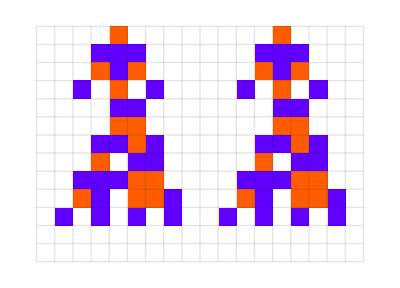
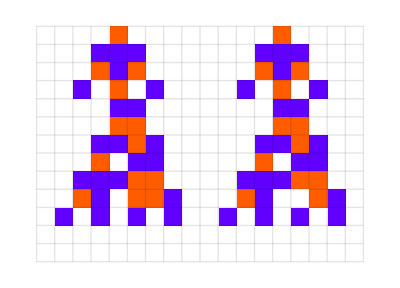
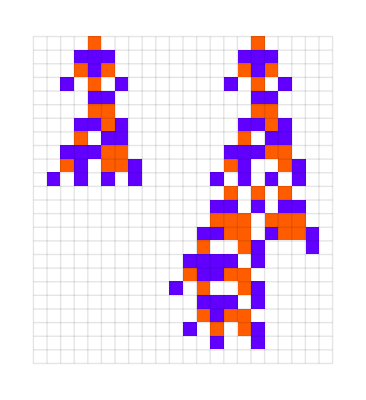
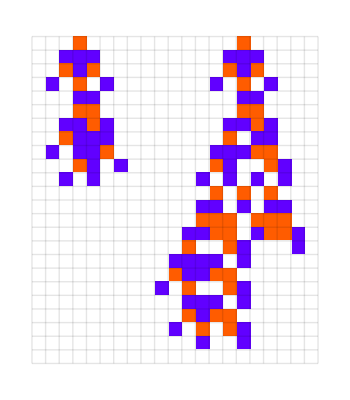
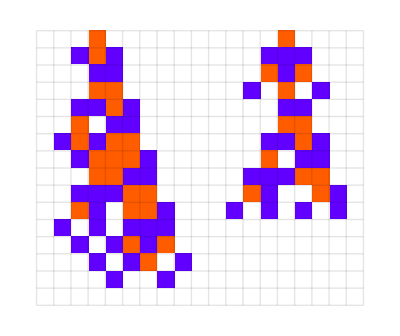
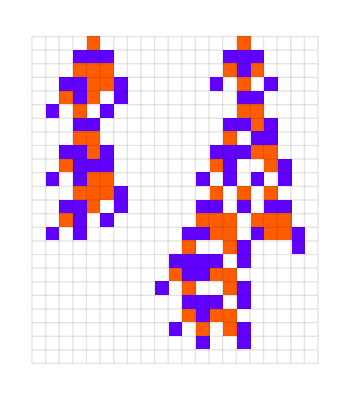
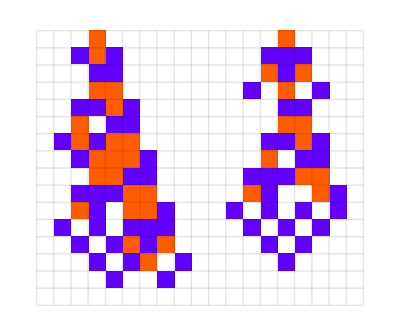
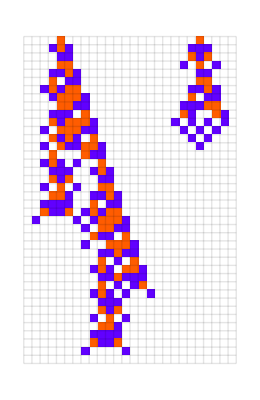
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
fossils = NestList[evo, pop, 8000];
gathered = GatherBy[fossils, Map[#[[2]]&, #, {2}]&];
Map[plotorg, First/@ gathered, {2}]
```

## All Possible Combs

```mathematica
r2 = {5586032023494,3,1};
```

```mathematica
r1 = {5593005590109,3,1};
```

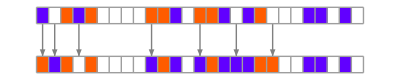

```mathematica
rulesmutationplot[{initrule,diffsmemo[[47, 21]] }]
```

```mathematica
locdiff[rule1_, rule2_]:= Block[{},
digs = Transpose[IntegerDigits[#[[1]], #[[2]], 27]&/@ {rule1, rule2}];
Position[digs,_List?(#[[1]] != #[[2]]&)]
]
```

```mathematica
allcombs[rule1_, rule2_]:= Block[{difflocs = DeleteCases[locdiff[rule1, rule2], {}]},
If[difflocs == {}, {},
locs = difflocs[[All, 1]];
Echo[locs];
subsets=Subsets[locs, {1, Length[locs]}];
d2 = todigs[rule2];
reps = Map[#->d2[[#]]&, subsets, {2}];
allgenes = ReplacePart[todigs[initrule], #]&/@ reps;
allrus = toru/@ allgenes
]]
```

```mathematica
idx = 0
```

0

14

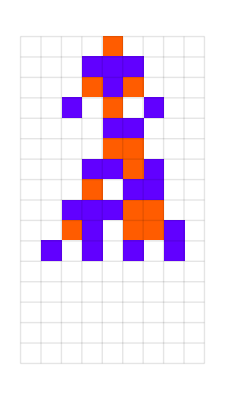
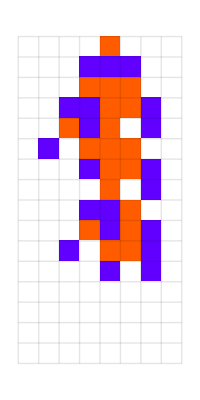

{1,2,4,6,10,16}

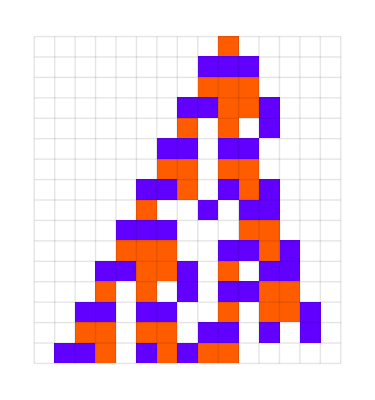
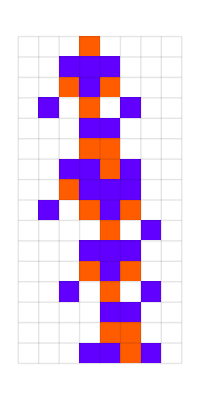
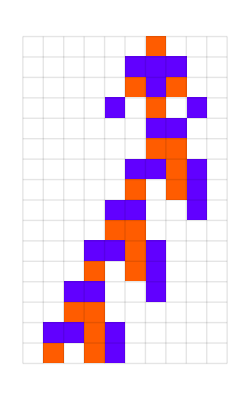
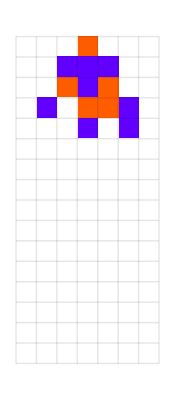
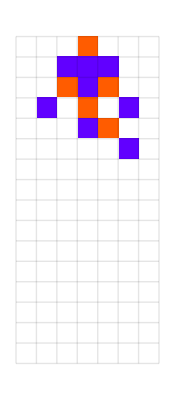
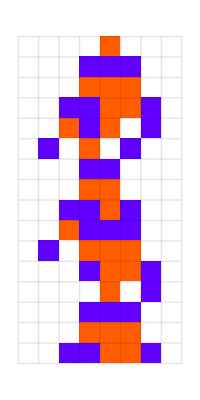
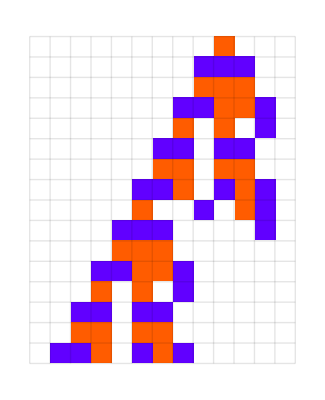
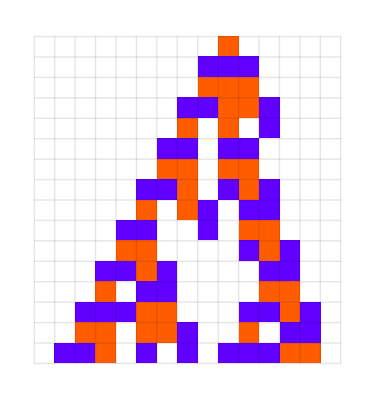
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
idx = 14
plot/@ {initrule, diffsmemo[[47, idx]]}
cs = allcombs[initrule, diffsmemo[[47, idx]]];
plot/@ cs
```

```mathematica
plot[cs[[25]]]
```

-Graphics-

```mathematica
r4 = cs[[25]]
```

{4738743234717,3,1}

```mathematica
plot/@ diffsmemo[[46]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
idx = idx+1;
plot/@ {diffsmemo[[46, idx]], r4}
cs = allcombs[diffsmemo[[46, idx]], r4];
plot/@ cs
lts = testlifetime/@ cs
```

12

{-Graphics-,-Graphics-}

{1,2,5,6,7,8,10,12,16,20}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[cs]
```

1023

```mathematica
testlifetime/@cs
```

{-∞,-∞,11,11,11,11,11,11,6,11,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,6,-∞,11,11,11,11,11,6,11,11,11,11,11,6,11,11,11,11,6,11,11,11,6,11,11,6,11,6,11,6,-∞,-∞,-∞,-∞,-∞,-∞,16,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,6,-∞,-∞,-∞,-∞,-∞,6,-∞,-∞,-∞,-∞,6,-∞,-∞,-∞,6,-∞,-∞,6,-∞,6,-∞,6,11,11,11,11,6,11,11,11,11,6,11,11,11,6,11,11,6,11,6,11,6,11,11,11,6,11,11,11,6,11,11,6,11,6,11,6,11,11,6,11,11,6,11,6,11,6,11,6,11,6,11,6,6,11,6,6,-∞,-∞,-∞,-∞,-∞,16,-∞,-∞,-∞,-∞,-∞,16,-∞,-∞,-∞,-∞,16,-∞,-∞,-∞,16,-∞,-∞,16,-∞,16,-∞,16,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,6,-∞,-∞,-∞,-∞,6,-∞,-∞,-∞,6,-∞,-∞,6,-∞,6,-∞,6,-∞,-∞,-∞,6,-∞,-∞,-∞,6,-∞,-∞,6,-∞,6,-∞,6,-∞,-∞,6,-∞,-∞,6,-∞,6,-∞,6,-∞,6,-∞,6,-∞,6,6,-∞,6,6,11,11,11,6,11,11,11,6,11,11,6,11,6,11,6,11,11,6,11,11,6,11,6,11,6,11,6,11,6,11,6,6,11,6,6,11,11,6,11,11,6,11,6,11,6,11,6,11,6,11,6,6,11,6,6,11,6,11,6,11,6,6,11,6,6,6,11,6,6,6,-∞,-∞,-∞,-∞,16,-∞,-∞,-∞,-∞,16,-∞,-∞,-∞,16,-∞,-∞,16,-∞,16,-∞,16,-∞,-∞,-∞,16,-∞,-∞,-∞,16,-∞,-∞,16,-∞,16,-∞,16,-∞,-∞,16,-∞,-∞,16,-∞,16,-∞,16,-∞,16,-∞,16,-∞,16,16,-∞,16,16,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,6,-∞,-∞,-∞,6,-∞,-∞,6,-∞,6,-∞,6,-∞,-∞,6,-∞,-∞,6,-∞,6,-∞,6,-∞,6,-∞,6,-∞,6,6,-∞,6,6,-∞,-∞,6,-∞,-∞,6,-∞,6,-∞,6,-∞,6,-∞,6,-∞,6,6,-∞,6,6,-∞,6,-∞,6,-∞,6,6,-∞,6,6,6,-∞,6,6,6,11,11,6,11,11,6,11,6,11,6,11,6,11,6,11,6,6,11,6,6,11,6,11,6,11,6,6,11,6,6,6,11,6,6,6,11,6,11,6,11,6,6,11,6,6,6,11,6,6,6,6,11,6,6,6,6,-∞,-∞,-∞,16,-∞,-∞,-∞,16,-∞,-∞,16,-∞,16,-∞,16,-∞,-∞,16,-∞,-∞,16,-∞,16,-∞,16,-∞,16,-∞,16,-∞,16,16,-∞,16,16,-∞,-∞,16,-∞,-∞,16,-∞,16,-∞,16,-∞,16,-∞,16,-∞,16,16,-∞,16,16,-∞,16,-∞,16,-∞,16,16,-∞,16,16,16,-∞,16,16,16,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,6,-∞,-∞,6,-∞,6,-∞,6,-∞,6,-∞,6,-∞,6,6,-∞,6,6,-∞,6,-∞,6,-∞,6,6,-∞,6,6,6,-∞,6,6,6,-∞,6,-∞,6,-∞,6,6,-∞,6,6,6,-∞,6,6,6,6,-∞,6,6,6,6,11,6,11,6,11,6,6,11,6,6,6,11,6,6,6,6,11,6,6,6,6,6,11,6,6,6,6,6,-∞,-∞,16,-∞,-∞,16,-∞,16,-∞,16,-∞,16,-∞,16,-∞,16,16,-∞,16,16,-∞,16,-∞,16,-∞,16,16,-∞,16,16,16,-∞,16,16,16,-∞,16,-∞,16,-∞,16,16,-∞,16,16,16,-∞,16,16,16,16,-∞,16,16,16,16,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,6,-∞,6,-∞,6,6,-∞,6,6,6,-∞,6,6,6,6,-∞,6,6,6,6,6,-∞,6,6,6,6,6,6,11,6,6,6,6,6,6,-∞,16,-∞,16,-∞,16,16,-∞,16,16,16,-∞,16,16,16,16,-∞,16,16,16,16,16,-∞,16,16,16,16,16,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,6,-∞,6,6,6,6,6,6,6,16,-∞,16,16,16,16,16,16,-∞,6,16}

```mathematica
lts = ReplaceAll[testlifetime/@ cs, -Infinity->0]
```

{0,0,11,11,11,11,11,11,6,11,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,11,11,11,11,11,6,11,11,11,11,11,6,11,11,11,11,6,11,11,11,6,11,11,6,11,6,11,6,0,0,0,0,0,0,16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,0,6,0,0,0,0,6,0,0,0,6,0,0,6,0,6,0,6,11,11,11,11,6,11,11,11,11,6,11,11,11,6,11,11,6,11,6,11,6,11,11,11,6,11,11,11,6,11,11,6,11,6,11,6,11,11,6,11,11,6,11,6,11,6,11,6,11,6,11,6,6,11,6,6,0,0,0,0,0,16,0,0,0,0,0,16,0,0,0,0,16,0,0,0,16,0,0,16,0,16,0,16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,6,0,0,0,6,0,0,6,0,6,0,6,0,0,0,6,0,0,0,6,0,0,6,0,6,0,6,0,0,6,0,0,6,0,6,0,6,0,6,0,6,0,6,6,0,6,6,11,11,11,6,11,11,11,6,11,11,6,11,6,11,6,11,11,6,11,11,6,11,6,11,6,11,6,11,6,11,6,6,11,6,6,11,11,6,11,11,6,11,6,11,6,11,6,11,6,11,6,6,11,6,6,11,6,11,6,11,6,6,11,6,6,6,11,6,6,6,0,0,0,0,16,0,0,0,0,16,0,0,0,16,0,0,16,0,16,0,16,0,0,0,16,0,0,0,16,0,0,16,0,16,0,16,0,0,16,0,0,16,0,16,0,16,0,16,0,16,0,16,16,0,16,16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,6,0,0,6,0,6,0,6,0,0,6,0,0,6,0,6,0,6,0,6,0,6,0,6,6,0,6,6,0,0,6,0,0,6,0,6,0,6,0,6,0,6,0,6,6,0,6,6,0,6,0,6,0,6,6,0,6,6,6,0,6,6,6,11,11,6,11,11,6,11,6,11,6,11,6,11,6,11,6,6,11,6,6,11,6,11,6,11,6,6,11,6,6,6,11,6,6,6,11,6,11,6,11,6,6,11,6,6,6,11,6,6,6,6,11,6,6,6,6,0,0,0,16,0,0,0,16,0,0,16,0,16,0,16,0,0,16,0,0,16,0,16,0,16,0,16,0,16,0,16,16,0,16,16,0,0,16,0,0,16,0,16,0,16,0,16,0,16,0,16,16,0,16,16,0,16,0,16,0,16,16,0,16,16,16,0,16,16,16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,6,0,6,0,6,0,6,0,6,0,6,6,0,6,6,0,6,0,6,0,6,6,0,6,6,6,0,6,6,6,0,6,0,6,0,6,6,0,6,6,6,0,6,6,6,6,0,6,6,6,6,11,6,11,6,11,6,6,11,6,6,6,11,6,6,6,6,11,6,6,6,6,6,11,6,6,6,6,6,0,0,16,0,0,16,0,16,0,16,0,16,0,16,0,16,16,0,16,16,0,16,0,16,0,16,16,0,16,16,16,0,16,16,16,0,16,0,16,0,16,16,0,16,16,16,0,16,16,16,16,0,16,16,16,16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,6,0,6,6,0,6,6,6,0,6,6,6,6,0,6,6,6,6,6,0,6,6,6,6,6,6,11,6,6,6,6,6,6,0,16,0,16,0,16,16,0,16,16,16,0,16,16,16,16,0,16,16,16,16,16,0,16,16,16,16,16,0,0,0,0,0,0,0,0,6,0,6,6,6,6,6,6,6,16,0,16,16,16,16,16,16,0,6,16}

```mathematica
ListPlot[lts]
```

-Graphics-

## Asexual vs. Sexual Three-color

### 1-gene

```mathematica
org
```

{{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438118980837975564,4,1},9}}

```mathematica
cut=200;
evo1=NestList[CompoundExpression[
new=muorg[#],
(*Echo[new],*)
kept = Table[ If[new[[i, 2]]>=#[[i , 2]], new[[i]], #[[i]]], {i, 1, 2}],
recombed = recomborg[kept]
]&,
org,1000];
evo2=Rest[First/@SplitBy[evo1,{#[[1, -1]], #[[2, -1]]}&]];
plotorg/@ evo2
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Two-gene

```mathematica
ngenes = 2;
norgs = 2;
nmutes = 2;
gene = {trirule, testlifetime[trirule]};
org = Table[gene, ngenes];
pop = Table[org, norgs];
```

```mathematica
newpop = mupop[pop]
```

{{{{109636419052937157723438118981911717388,4,1},-∞},{{109636419052937157723440370780651660812,4,1},9}},{{{109636419052937157723438118980841121292,4,1},9},{{108307191057152241850534311920557630988,4,1},-∞}}}

```mathematica
selected = Table[ If[newpop[[i, j, 2]]>=pop[[i , j, 2]], newpop[[i, j]], pop[[i, j]]], {i, 1, norgs}, {j, 1, ngenes}]
```

{{{{109636419052937157723438118980837975564,4,1},11},{{109636419052937157723438118980837975564,4,1},11}},{{{109636419052937157723438118980837975564,4,1},11},{{109636419052937157723438118980837975564,4,1},11}}}

```mathematica
evo[pop_]:= Block[{},
newpop = mupop[pop];
selected = Table[ If[newpop[[i, j, 2]]>=pop[[i , j, 2]], newpop[[i, j]], pop[[i, j]]], {i, 1, norgs}, {j, 1, ngenes}];
recombed = recomb[selected];
(*Echo[plotpop/@ {newpop, selected }];*)
selected
]
```

```mathematica
plotpop[pop]
```

{-Graphics-,-Graphics-}

```mathematica
pop[[1, 1, 2]]
```

11

```mathematica
plotpop[fossils[[10]]]
```

{-Graphics-,-Graphics-}

```mathematica
fossils = NestList[evo, pop, 500];
gathered = GatherBy[fossils, Map[#[[2]]&, #, {2}]&];
Map[plotorg, First/@ gathered, {2}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

## General Evo Function

```mathematica
selectfit[pop_, mu_]:= Table[ If[mu[[i, j, 2]]>=pop[[i , j, 2]], mu[[i, j]], pop[[i, j]]], {i, 1, Length[pop]}, {j, 1, Length[pop[[1]]]}];
```

```mathematica
evo[init_, steps_]:= Block[{},
NestList[adapt, init, steps]
]
```

```mathematica
adapt[{pop_, mufunc_, fitfunc_, recomfunc_}]:= Block[{mu, fit, recom},
mu = mufunc[pop, fitfunc, 2];
fit = selectfit[pop, mu];
recom = If[SameQ[recomfunc,None], fit, recomfunc[fit]];
{recom, mufunc, fitfunc, recomfunc}
]
```

```mathematica
pop = {org}
```

{{{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438118980837975564,4,1},9}}}

```mathematica
adapt[{pop, mupop, testlifetime[#, 200]&, recomborgs}]
```

{{{{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438118980837975564,4,1},9}}},mupop,testlifetime[#1,200]&,recomborgs}

```mathematica
paths = Table[evo[{pop, mupop, testlifetime[#, 250]&, recomborgs},4000], 5];
```

$Aborted

```mathematica
idx = 3;
path = paths[[1]];
```

```mathematica
path = evo[{pop, mupop, testlifetime[#, 250]&, recomborgs},1000];
gathered = GatherBy[path[[All, 1]], Map[#[[2]]&, #, {2}]&];
maxlife =Total[gathered[[-1, 1, 1, All, 2]]]
Map[plotorg, First/@ gathered, {2}]
```

462

```mathematica
paths[[All,;;10, 1]]
```

{{{{{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438118980837975564,4,1},9}}},{{{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438048612093797900,4,1},9}}},{{{{109636419052937157871012071570514388492,4,1},9},{{109636419052937157723438189349582153228,4,1},9}}},{{{{109636419052937157871012071570514388492,4,1},9},{{88368771120378503756977276385096640012,4,1},9}}},{{{{109636419052937157870723841194362676748,4,1},9},{{88368771120378503756977276385099785740,4,1},9}}},{{{{109636419052937157870723841194362676748,4,1},9},{{88368771120378503756977276385099785740,4,1},9}}},{{{{109636419052937157870723841194362676748,4,1},9},{{88368771120378503756977276385099785740,4,1},9}}},{{{{109636419052937157944510817489200883212,4,1},9},{{88202617620905389272864300502564742668,4,1},9}}},{{{{109636419052937157944510782304828794380,4,1},9},{{88202617640712429901430384900950730252,4,1},9}}},{{{{109636419052937157944510782302681310732,4,1},10},{{88202617640712434623796867770595943948,4,1},9}}}},{{{{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438118980837975564,4,1},9}}},{{{{88368771120378503756977206016352462348,4,1},9},{{109636419092551238980570287777609950732,4,1},9}}},{{{{88368771120378503756977197220259440140,4,1},9},{{109636581351828068193933679355620238860,4,1},9}}},{{{{88368771120378503756977162035887351308,4,1},9},{{109636581351828068193933679355620238860,4,1},9}}},{{{{88368771120378503756977724985840772620,4,1},10},{{109636581351828068193934523780550370828,4,1},9}}},{{{{88368771120378503756977724985840772620,4,1},10},{{125587317301247058668780208503914505740,4,1},9}}},{{{{88368772388029103985207126482543977996,4,1},10},{{125587317301247058668780208503914767884,4,1},10}}},{{{{88368774923330304441665929475950388748,4,1},10},{{125587317301247058668780208503914767884,4,1},10}}},{{{{88368774923330304450889301512805164556,4,1},10},{{125587318568897658897009610000617973260,4,1},10}}},{{{{88368774923330304451177531888956876300,4,1},10},{{125587318568897658897009610000617973260,4,1},10}}}},{{{{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438118980837975564,4,1},9}}},{{{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438118980841121292,4,1},9}}},{{{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723402090183822157324,4,1},9}}},{{{{109636419052879129284096616780452079116,4,1},9},{{109636419052937157723402090183822157324,4,1},9}}},{{{{109636419052879129284096616780452079116,4,1},9},{{109636419052937157723402090183822159372,4,1},9}}},{{{{109636419033072088655530532382066091532,4,1},9},{{109636419052936251029037379211941129740,4,1},9}}},{{{{109636419033072088655530532382066091532,4,1},9},{{109636419052936251030190300716547976716,4,1},9}}},{{{{109636419033072088655530532382066091532,4,1},9},{{109636419052936251030190300716547976716,4,1},9}}},{{{{109636581292348917868893923960076379660,4,1},9},{{109636419052936251030190300716547976716,4,1},9}}},{{{{130904229224907571835354836924561892876,4,1},9},{{109636419052936251030190300716547976716,4,1},9}}}},{{{{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438118980837975564,4,1},9}}},{{{{109636419052937157723438118980837976588,4,1},9},{{109636419052937157723438681930791396876,4,1},10}}},{{{{109636419052937157723438118980837976588,4,1},9},{{109636419052937157723438681930793494028,4,1},11}}},{{{{109636419052937157723438118980839025164,4,1},9},{{109636419052937157723438681930793494028,4,1},11}}},{{{{109636419052937157723438118980839041548,4,1},9},{{109636439335346761375109105878044780044,4,1},11}}},{{{{109636419092551238980570287777611016716,4,1},9},{{109636439335346761375109105878044780044,4,1},11}}},{{{{109636419092551238994405345832893180428,4,1},9},{{109636439335346761375109105878044780044,4,1},11}}},{{{{109636419092551238994405345832893180428,4,1},9},{{109636439335346761375109105878044780044,4,1},11}}},{{{{109636419092551238980570287777611016716,4,1},9},{{109636439335346761375109105878044780044,4,1},11}}},{{{{109470265593078124496457311895075973644,4,1},9},{{109636439335346761375109106084203210252,4,1},11}}}},{{{{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438118980837975564,4,1},9}}},{{{{109636419052941993426716577497536800268,4,1},9},{{109636459617756365026778966875340547596,4,1},9}}},{{{{109636094534388334999989794341516224012,4,1},9},{{109636459617756365026778966875340563980,4,1},9}}},{{{{109636094534388337361173035776338830860,4,1},9},{{109636459617756365026778966875340563980,4,1},9}}},{{{{109636094534388337361173035776338830860,4,1},9},{{109636459617756365031390652893767951884,4,1},9}}},{{{{109630902237529802533544505280009610764,4,1},9},{{109636459617756365031390617709395863052,4,1},9}}},{{{{109630902237529802533544506379521238540,4,1},9},{{109636439335346761379720193762144577036,4,1},9}}},{{{{110960130233314718406448313439801583116,4,1},9},{{109636439335346761379721038187074709004,4,1},9}}},{{{{110960130233314718406448313439801583116,4,1},9},{{109470285835873646895608062304539665932,4,1},9}}},{{{{110960130233314718406448313422621713932,4,1},9},{{109470285835873646895608062304535471628,4,1},9}}}},{{{{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438118980837975564,4,1},9}}},{{{{109635770015829840869984552668796823052,4,1},9},{{109636419055413037802008879530636224012,4,1},9}}},{{{{109635770015829840869984552668796823052,4,1},9},{{109636419055413037802008879530639369740,4,1},9}}},{{{{109635932275106670083347944246807111180,4,1},9},{{109636419055413037949582832120315782668,4,1},9}}},{{{{109635932275106670083347944246807111180,4,1},9},{{109636419055413037949582832120315782668,4,1},9}}},{{{{109635932275106670083347944246807111180,4,1},9},{{109636419055413038539878642479021434380,4,1},9}}},{{{{109635932277582550161918704796605359628,4,1},9},{{88368771122854384573417729514535921164,4,1},9}}},{{{{109635932277582550161918704796605359628,4,1},9},{{88368771122854384573417729514523338252,4,1},9}}},{{{{109635932277582550161918704796605359628,4,1},9},{{99002595089133711556648185996766094860,4,1},9}}},{{{{109635932273868730044062563971907986956,4,1},9},{{99002595089133711556648133220207961612,4,1},9}}}},{{{{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438118980837975564,4,1},9}}},{{{{109636419052937157723402090183819011596,4,1},9},{{109636419052937157723438118980837975564,4,1},9}}},{{{{109636419052937157722825629431515588108,4,1},9},{{109636419052937157723442622580465346060,4,1},9}}},{{{{109636419052937157722830133031142958604,4,1},9},{{109636094534383499296715839424444769804,4,1},9}}},{{{{109636500182575572329511828820148102668,4,1},9},{{109636094534383499296715839424444769804,4,1},9}}},{{{{109636500182575572329511793635776013836,4,1},9},{{109636094534383499296715839372905162252,4,1},9}}},{{{{109636500182575572329511864004520191500,4,1},9},{{109636094534383499296715909741649339916,4,1},9}}},{{{{109636500182575572329511864004521240076,4,1},9},{{109636094534383499296715909741112469004,4,1},15}}},{{{{109636500182556229516398029937725941260,4,1},9},{{109636094534383499296715909792652076556,4,1},15}}},{{{{109636500182556229221250124758373115404,4,1},9},{{109636094534383499296715909792652076556,4,1},15}}}},{{{{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438118980837975564,4,1},9}}},{{{{109636419052937157725743961990051669516,4,1},9},{{109636419052937158018586024160190801420,4,1},9}}},{{{{109636419052937158906335582707462972940,4,1},9},{{109636419052937158018586024160190801420,4,1},9}}},{{{{109636419052937158906335582707462971916,4,1},9},{{109636419052937158018586024160190801420,4,1},9}}},{{{{109636419052937158905182661202856124940,4,1},9},{{109636419052937158018586024160190801420,4,1},9}}},{{{{109470265553464044421069685320321081868,4,1},9},{{109636419052937158018586024160190801420,4,1},9}}},{{{{109470265555939924499640445870119330316,4,1},9},{{109636419052937158018586024160193947148,4,1},9}}},{{{{109470265555939924499640445870119334412,4,1},9},{{109636419052937158018581520560566576652,4,1},9}}},{{{{109470265555939924499640445870115140108,4,1},9},{{109636419052937158018581450191822398988,4,1},9}}},{{{{109470265555939924499631438670860399116,4,1},9},{{109636419052937158018581450191822398988,4,1},9}}}},{{{{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438118980837975564,4,1},9}}},{{{{109636419052937157723726349356989687308,4,1},9},{{109636419052937157723438118980838499852,4,1},10}}},{{{{109636419052937157723726349356989687308,4,1},9},{{109636419052937157723438118980033193484,4,1},10}}},{{{{109636419052705043966360340555446101516,4,1},9},{{109636419052937157723438118980033197580,4,1},10}}},{{{{109636419052705043966360340624165578252,4,1},9},{{109636419052937157723438118980033197580,4,1},10}}},{{{{109636419052705044113934293213841991180,4,1},9},{{109636419052937157871012071569709610508,4,1},10}}},{{{{109636419052705044113934293213842040332,4,1},9},{{109636419052937157871012071569709610508,4,1},10}}},{{{{109636419052705044113934293213842040332,4,1},9},{{109636419052937157871012071569709610508,4,1},10}}},{{{{109636419052705044113934293213842040332,4,1},9},{{109636419052937157871012071569709610508,4,1},10}}},{{{{109636419052705044113934293213845186060,4,1},9},{{109636419052937157871012071569709610508,4,1},10}}}},{{{{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438118980837975564,4,1},9}}},{{{{109636419052937157723438118980837975564,4,1},9},{{109636419052937157723438118980837975564,4,1},9}}},{{{{109636419052937157723438681930791396876,4,1},10},{{109636419052937138833972187502257120780,4,1},9}}},{{{{109636419052937157723438681930791396876,4,1},10},{{109636419052937138833972187502257120780,4,1},9}}},{{{{109636419092551238980570850727563372044,4,1},10},{{109636419052937138833972187502257120780,4,1},9}}},{{{{109636419092551220091104919248982517260,4,1},10},{{109636419052937138833972187502257120780,4,1},9}}},{{{{109636419092551220091104919248982517260,4,1},10},{{109636419052937138833972187502257120780,4,1},9}}},{{{{109636419092550615628195111934395164172,4,1},10},{{109636419052937138833972187502257645068,4,1},10}}},{{{{109636419092551220091104919248982517260,4,1},10},{{109636419052936534371062380187670291980,4,1},10}}},{{{{109636419092551220091104919248982517260,4,1},10},{{109636419052897848744834712054079694348,4,1},10}}}}}

```mathematica
pathsmemo = paths[[All, All, 1]];
```

```mathematica
pathsmemo = {pathsmemo}
```

```mathematica
AppendTo[pathsmemo, paths[[All, All, 1]]];
```

```mathematica
Length[pathsmemo[[1]]]
```

1001

```mathematica
paths2 = pathsmemo[[2]];
```

```mathematica
Total/@pathsmemo[[1, 1]][[All, 1, All, 2]]
```

```mathematica
tp = ListLinePlot[Transpose[#[[All, 1, All, 2]]], PlotHighlighting->None, PlotRange->200]&/@ pathsmemo[[5]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sum = ListLinePlot[Total/@#[[All, 1, All, 2]], PlotHighlighting->None, PlotRange->400]&/@ pathsmemo[[5]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
col = RGBColor[0.2,0.59,0.16];
```

```mathematica
tp2 = ListLinePlot[Transpose[#[[All, 1, All, 2]]], PlotHighlighting->None, PlotStyle->col, PlotRange->200]&/@ pathsmemo[[4]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sum2 = ListLinePlot[Total/@#[[All, 1, All, 2]], PlotHighlighting->None, PlotStyle->col, PlotRange->400]&/@ pathsmemo[[4]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[tp[[#]], tp2[[#]]]&/@ Range[5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[sum[[#]], sum2[[#]]]&/@ Range[5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### 2-color

## Climbing 1 by 1 1000 steps

### Running

```mathematica
selectfit[pop_, mu_]:= Table[ If[mu[[i, j, 2]]==pop[[i , j, 2]]+1|| mu[[i, j, 2]]==pop[[i , j, 2]], mu[[i, j]], pop[[i, j]]], {i, 1, Length[pop]}, {j, 1, Length[pop[[1]]]}];
adaptroad[{pop_, mufunc_, fitfunc_, recomfunc_}]:= Block[{mu, fit, recom},
mu = mufunc[pop, fitfunc, 2];
fit = selectfit[pop, mu];
recom = If[SameQ[recomfunc,None], fit, recomfunc[fit]];
{recom, mufunc, fitfunc, recomfunc}
]
evoroad[init_, steps_]:= Block[{},
NestList[adaptroad, init, steps]
]
```

```mathematica
org = {{tri2, testlifetime[tri2]}, {tri2, testlifetime[tri2]}};
pop = {org};
```

```mathematica
plotpop@pop
```

{-Graphics-}

```mathematica
path[[All, 1, 1, All,2]]
```

{{1,1},{1,1},{1,1},{1,1},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{3,3},{3,3},{3,3},{3,3},{3,3},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{7,7},{8,8},{8,8},{8,8},{8,8},{8,8},{8,8},{8,8},{8,8},{8,8},{8,8},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{9,9},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{10,10},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{11,11},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{12,12},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{13,13},{14,14},{14,14},{14,14},{14,14},{14,14},{14,14},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{15,15},{16,16},{16,16},{16,16},{16,16},{16,16},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{17,17},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{18,18},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{19,19},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{20,20},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{21,21},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{22,22},{23,23},{23,23},{23,23},{23,23},{23,23},{24,24},{24,24},{24,24},{24,24},{24,24},{24,24},{24,24},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{25,25},{26,26},{26,26},{26,26},{26,26},{27,27},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{29,29},{30,30},{30,30},{30,30},{30,30},{30,30},{30,30},{30,30},{30,30},{30,30},{30,30},{30,30},{30,30},{30,30},{30,30},{30,30},{30,30},{30,30},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{31,31},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32},{32,32}}

```mathematica
paths = Table[evoroad[{pop, mupop, testlifetime[#, 50]&, None},1000], 10];
```

```mathematica
{time, path} = Timing[evoroad[{pop, mupop, testlifetime[#, 50]&, recomborgs},4000]];
```

```mathematica
path = pathsmemo[[8]];
```

```mathematica
gathered = GatherBy[path[[All, 1]], Map[#[[2]]&, #, {2}]&];
maxlife =Total[gathered[[-1, 1, 1, All, 2]]];
Map[plotorg, First/@ gathered, {2}]
```

{{-Graphics-}}

```mathematica
tp = ListLinePlot[Transpose[path[[All, 1,1, All, 2]]], PlotHighlighting->None, PlotRange->30]
```

-Graphics-

```mathematica
AppendTo[pathsmemo, paths[[All, All, 1]]];
```

### graphing asexual vs. sexual

#### Asexual

```mathematica
tp = ListLinePlot[Transpose[#[[All, 1, All, 2]]], PlotHighlighting->None, PlotRange->30]&/@ pathsmemo[[7]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Sexual

```mathematica
tp2 = ListLinePlot[Transpose[#[[All, 1, All, 2]]], PlotHighlighting->None, PlotStyle->col, PlotRange->30]&/@ pathsmemo[[6]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Both

```mathematica
Show[tp[[#]], tp2[[#]]]&/@ Range[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Sums

```mathematica
sum = ListLinePlot[Total/@#[[All, 1, All, 2]], PlotHighlighting->None, PlotRange->60]&/@ pathsmemo[[7]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sum2 = ListLinePlot[Total/@#[[All, 1, All, 2]], PlotHighlighting->None, PlotStyle->col, PlotRange->60]&/@ pathsmemo[[6]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[sum[[#]], sum2[[#]]]&/@ Range[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Climbing 1 by 1 2000 steps

```mathematica
recomfunc = recomborgs;
```

```mathematica
selectfit[pop_, mu_]:= Table[ If[mu[[i, j, 2]]==pop[[i , j, 2]]+1|| mu[[i, j, 2]]==pop[[i , j, 2]], mu[[i, j]], pop[[i, j]]], {i, 1, Length[pop]}, {j, 1, Length[pop[[1]]]}];
adaptroad2[pop_]:= Block[{mu, fit, recom},
mu = mupop2[pop];
fit = selectfit[pop, mu];
recom = If[SameQ[recomfunc,None], fit, recomfunc[fit]]
]
evoroad2[init_, steps_]:= Block[{},
NestList[adaptroad2, init, steps]
]
```

```mathematica
{time, path} = Timing[evoroad2[pop, 1000]];
```

```mathematica
paths = Table[evoroad[{pop, mupop, testlifetime[#, 40]&, recomborgs},2000], 10];
```

```mathematica
AppendTo[pathsmemo, paths[[All, All, 1]]];
```

```mathematica
gathered = GatherBy[path, Map[#[[2]]&, #, {2}]&];
maxlife =Total[gathered[[-1, 1, 1, All, 2]]]
Map[plotorg, First/@ gathered, {2}]
```

42

{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

### graphing asexual vs. sexual

#### Asexual

```mathematica
tp = ListLinePlot[Transpose[#[[All, 1, All, 2]]], PlotHighlighting->None, PlotRange->50]&/@ pathsmemo[[8]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Sexual

```mathematica
tp2 = ListLinePlot[Transpose[#[[All, 1, All, 2]]], PlotHighlighting->None, PlotStyle->col, PlotRange->50]&/@ pathsmemo[[9]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Both

```mathematica
Show[tp[[#]], tp2[[#]]]&/@ Range[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Sums

```mathematica
sum = ListLinePlot[Total/@#[[All, 1, All, 2]], PlotHighlighting->None, PlotRange->100]&/@ pathsmemo[[8]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sum2 = ListLinePlot[Total/@#[[All, 1, All, 2]], PlotHighlighting->None, PlotStyle->col, PlotRange->100]&/@ pathsmemo[[9]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[sum[[#]], sum2[[#]]]&/@ Range[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## 1 by 1 two-color

```mathematica
ngenes = 2;
norgs = 1;
nmutes = 2;
gene = {initrule, testlifetime[initrule]};
org = Table[gene, ngenes];
pop = Table[org, norgs];
```

### Running

```mathematica
selectfit[pop_, mu_]:= Table[ If[mu[[i, j, 2]]==pop[[i , j, 2]]+2 || mu[[i, j, 2]]==pop[[i , j, 2]]+1|| mu[[i, j, 2]]==pop[[i , j, 2]], mu[[i, j]], pop[[i, j]]], {i, 1, Length[pop]}, {j, 1, Length[pop[[1]]]}];
adaptroad[{pop_, mufunc_, fitfunc_, recomfunc_}]:= Block[{mu, fit, recom},
mu = mufunc[pop, fitfunc, 2];
fit = selectfit[pop, mu];
recom = If[SameQ[recomfunc,None], fit, recomfunc[fit]];
{recom, mufunc, fitfunc, recomfunc}
]
evoroad[init_, steps_]:= Block[{},
NestList[adaptroad, init, steps]
]
```

```mathematica
pop = {{{{0, 4, 1}, 1}, {{0, 4, 1},1}}}
```

{{{{0,4,1},1},{{0,4,1},1}}}

```mathematica
plotpop@pop
```

{-Graphics-}

```mathematica
paths = Table[evoroad[{pop, mupop, testlifetime[#, 50]&, recomborgs},4000], 10];
```

```mathematica
{time, path} = Timing[evoroad[{pop, mupop, testlifetime[#, 50]&, recomborgs}, 4000]];
```

```mathematica
path = pathsmemo[[8]];
```

```mathematica
gathered = GatherBy[path[[2]], Map[#[[2]]&, #, {2}]&];
changes = First/@gathered;
maxlife =Total[gathered[[-1, 1, 1, All, 2]]];
Map[plotorg, First/@ gathered, {2}]
```

{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
Length/@ pathsmemo
```

{10,10,10,5,5,10,10,10,10,10,10,10,10,10,10,10}

```mathematica
tp = ListLinePlot[Transpose[path[[All, 1,1, All, 2]]], PlotHighlighting->None, PlotRange->30]
```

-Graphics-

```mathematica
AppendTo[pathsmemo, paths[[All, All, 1]]];
```

```mathematica
Length@pathsmemo
```

16

### graphing asexual vs. sexual

#### Asexual

```mathematica
tp = ListLinePlot[Transpose[#[[All, 1, All, 2]]], PlotHighlighting->None, PlotRange->50]&/@ pathsmemo[[15]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Sexual

```mathematica
Length[pathsmemo]
```

14

```mathematica
tp2 = ListLinePlot[Transpose[#[[All, 1, All, 2]]], PlotHighlighting->None, PlotStyle->col, PlotRange->50]&/@ pathsmemo[[16]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Both

```mathematica
Show[tp[[#]], tp2[[#]]]&/@ Range[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Sums

```mathematica
sum = ListLinePlot[Total/@#[[All, 1, All, 2]], PlotHighlighting->None, PlotRange->60]&/@ pathsmemo[[10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sum2 = ListLinePlot[Total/@#[[All, 1, All, 2]], PlotHighlighting->None, PlotStyle->col, PlotRange->60]&/@ pathsmemo[[11]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[sum[[#]], sum2[[#]]]&/@ Range[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## One color asex vs sex

```mathematica
Module[{init={1,1,1,0,1,1,1},g0,gfixed,probs},
gfixed=Graph[Join[ReplaceAll[EdgeList[{{"[◼]", "MutationGraph"}}[2,1]],
UndirectedEdge[x_,y_]:>Splice[{DirectedEdge[x,y],DirectedEdge[y,x]}]],{-1->0},
#->Square[#]&/@VertexList[{{"[◼]", "MutationGraph"}}[2,1]]]];
probs=Association[
Thread[VertexList[{{"[◼]", "MutationGraph"}}[2,1]
]->ResourceFunction["DirectedGraphTransferMatrix"][
gfixed,Square[#]&/@VertexList[{{"[◼]", "MutationGraph"}}[2,1]],{-1}][[All,1]]]];

g0=ResourceFunction["FixedPointGraph"][
{{"[◼]", "IterateMutations"}}[1,GreaterEqual][#,init]&,
{{{0,2,1},1}}];
Graph[g0,
GraphLayout->{"LayeredDigraphEmbedding","RootVertex"->{{0,2,1},1}},
EdgeStyle->Gray,
VertexShapeFunction->Function[
Inset[ArrayPlot[CellularAutomaton[Echo[#2[[1]]],
Join[{0},init,{0}]
,#2[[2]]],Mesh->True,MeshStyle->Opacity[.1],ImageSize->{Automatic,6(#2[[2]]+1)^.9},
ColorRules->{1->Blend[{Red,Black},Rescale[probs[#2[[1,1]]],MinMax[Values[probs]]]],0->White}
],#1]],
PerformanceGoal->"Quality"]
]
```

{0,2,1}
{4,2,1}
{8,2,1}
{32,2,1}
{64,2,1}
{128,2,1}
{40,2,1}
{72,2,1}
{96,2,1}
{136,2,1}
{160,2,1}
{192,2,1}
{104,2,1}
{168,2,1}
{224,2,1}

-Graphics-

```mathematica
CellularAutomaton[Echo[{4,2,1}],Join[{0},{1,1,1,0,1,1,1},{0}],10]
```

{4,2,1}

{{0,1,1,1,0,1,1,1,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

```mathematica
getca[{168,2,1}]
```

{{1},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
CellularAutomaton[{168,2,1}, initconditions, nsteps]
```

{{1},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
{0,2,1}
{4,2,1}
{8,2,1}
{32,2,1}
{64,2,1}
{128,2,1}
{40,2,1}
{72,2,1}
{96,2,1}
{136,2,1}
{160,2,1}
{192,2,1}
{104,2,1}
{168,2,1}
{224,2,1}
```

```mathematica
plot[{104,2,1}, "init"->{0, 1,1,1,0,1,1,1, 0}, ColorRules->Automatic]
```

-Graphics-

```mathematica
getca[{224,2,1}, {0, 1,1,1,0,1,1,1, 0}, 10]
```

{{0,1,1,1,0,1,1,1,0},{0,0,1,1,1,0,1,1,0},{0,0,0,1,1,1,0,1,0},{0,0,0,0,1,1,1,0,0},{0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

```mathematica
ArrayPlot[{104,2,1}]
```

-Graphics-

```mathematica
g0=ResourceFunction["FixedPointGraph"][
{{"[◼]", "IterateMutations"}}[1,GreaterEqual][#,{1,1,1,0,1,1,1}]&,
{{{0,2,1},1}}]
```

-Graphics-

```mathematica
vs = VertexList@g0
```

{{{0,2,1},1},{{4,2,1},1},{{8,2,1},2},{{32,2,1},2},{{64,2,1},2},{{128,2,1},2},{{40,2,1},3},{{72,2,1},2},{{96,2,1},3},{{136,2,1},3},{{160,2,1},4},{{192,2,1},3},{{104,2,1},5},{{168,2,1},6},{{224,2,1},6}}

```mathematica
plot[#, "init"->{0, 1,1,1,0,1,1,1, 0}, ColorRules->Automatic]& /@ vs[[All, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Column[Module[
{deep=5000,cut=50,ru,life,evo,data,init={1,1,1,0,1,1,1}},
ParallelTable[SeedRandom[426777+i];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,init,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,2,3/2},1},deep];
evo=First/@SplitBy[evo,Last];
GraphicsRow[Map[CompoundExpression[
data=CellularAutomaton[
First[#],{init,0},Last[#]+2],
data=ArrayPad[#,2]&/@data,
{{"[◼]", "SerratedBricksArrayPlot"}}[data,
ImageSize->{Automatic,14Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
]
]&,
evo]],{i,{3,2,5,21}}]
]]
```

```mathematica
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,init,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,2,3/2},1},deep];
evo=First/@SplitBy[evo,Last];
```

```mathematica
ngenes = 2;
norgs = 1;
nmutes = 2;
gene = {initrule, testlifetime[initrule]};
org = Table[gene, ngenes];
pop = Table[org, norgs];
```

```mathematica
path = evo[{pop, mupop, testlifetime[#, 250]&, recomborgs},1000];
gathered = GatherBy[path[[All, 1]], Map[#[[2]]&, #, {2}]&];
maxlife =Total[gathered[[-1, 1, 1, All, 2]]]
Map[plotorg, First/@ gathered, {2}]
```

## Lifetime Sequence

## Feature space plot

```mathematica
Module[{res,lifetimes,sublevels,drf,hts},
SeedRandom[1234];
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2],
{"Lifetimes","SubLevels"}];
lifetimes=res[[2,1,1,1]];
sublevels=res[[2,2,1,1]];
drf=DimensionReduction[IntegerDigits[#,2,16]&/@Keys[lifetimes],Method->"TSNE"];
ListPlot[KeyValueMap[Callout[#2,Framed[{{"[◼]", "SerratedBricksArrayPlot"}}[CellularAutomaton[{#1,2,3/2},{{1,1,1,0,1,1,1},0},1+{{"[◼]", "TestLifetime"}}[{#,2,3/2},{1,1,1,0,1,1,1}]],ImageSize->28],FrameStyle->None],LabelVisibility->All,Background->None]&,AssociationThread[#,drf[IntegerDigits[#,2,16]&/@#]]&@(First/@Values@sublevels)],PlotStyle->PointSize[0.001],Axes->None,Frame->True,FrameTicks->None,PlotRangePadding->{{1,7},{2,4}}]
]
```

```mathematica
selectfit[pop_, mu_]:= Table[ If[mu[[i, j, 2]]==pop[[i , j, 2]]+1|| mu[[i, j, 2]]==pop[[i , j, 2]], mu[[i, j]], pop[[i, j]]], {i, 1, Length[pop]}, {j, 1, Length[pop[[1]]]}];
adapt[{pop_, mufunc_, fitfunc_, recomfunc_}]:= Block[{mu, fit, recom},
recom = If[SameQ[recomfunc,None], pop, recomfunc[pop]];
mu = mufunc[recom, fitfunc, 2];
fit = selectfit[pop, mu];
{fit, mufunc, fitfunc, recomfunc}
]
evo[init_, steps_]:= Block[{},
NestList[adapt, init, steps]
]
```

```mathematica
ngenes = 2;
norgs = 1;
gene = {trirule, testlifetime[trirule]};
org = Table[gene, ngenes];
pop = Table[org, norgs];
```

```mathematica
apath = evo[{pop, mupop, testlifetime[#, 50]&, None},2000];
spath = evo[{pop, mupop, testlifetime[#, 50]&, recomborgs},2000];
```

```mathematica
phenopaths = {};
```

```mathematica
AppendTo[phenopaths, apath]
```

```mathematica
AppendTo[phenopaths, spath];
```

```mathematica
g1 = GatherBy[apath[[All, 1]], Map[#[[2]]&, #, {2}]&];
```

```mathematica
s = GatherBy[spath[[All, 1]], Map[#[[2]]&, #, {2}]&];
```

```mathematica
sg = (First/@ s)[[All, All, All,1, 1]];
```

```mathematica
g = (First/@ g1)[[All, All, All,1, 1]];
```

```mathematica
adr = DimensionReduction[IntegerDigits[#,4,64]&/@Flatten[g],Method->"TSNE"];
sdr = DimensionReduction[IntegerDigits[#,4,64]&/@Flatten[sg],Method->"TSNE"];
```

```mathematica
drs = adr[IntegerDigits[#,4,64]]&/@ g[[All, 1, 1]];
drs2 = adr[IntegerDigits[#,4,64]]&/@ g[[All, 1, 2]];
```

```mathematica
drs3 =  sdr[IntegerDigits[#,4,64]]&/@ sg[[All, 1, 1]];
drs4 =  sdr[IntegerDigits[#,4,64]]&/@ sg[[All, 1, 2]];
```

```mathematica
z1s = testlifetime[{#, 4, 1}]&/@ g[[All, 1, 1]];
z2s =  testlifetime[{#, 4, 1}]&/@ g[[All, 1, 2]];
z3s = testlifetime[{#, 4, 1}]&/@ sg[[All, 1, 1]];
z4s = testlifetime[{#, 4, 1}]&/@ sg[[All, 1, 2]];
```

```mathematica
c1 = MapThread[Append[#1, #2]&, {drs, z1s}];
c2 =  MapThread[Append[#1, #2]&, {drs2, z2s}];
```

```mathematica
c3 = MapThread[Append[#1, #2]&, {drs3, z3s}];
c4 =  MapThread[Append[#1, #2]&, {drs4, z4s}];
```

```mathematica
idxs = All;
```

```mathematica
ListLinePlot3D[{c3, c4}, PlotRange->All, PlotStyle->{Red, green}]
```

-Graphics3D-

```mathematica
ListLinePlot[{drs3, drs4}]
```

-Graphics-

```mathematica
PlotStyle->RGBColor[0.2,0.59,0.16]
```

```mathematica
Map[plotorg, First/@ g1[[;;100]], {2}]
```

{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

## Uncertainty Model

```mathematica
start = 5; 
max = 10;
angle = 1/2;
width = 10;
seg = 10;
lifetime = 4;
rad = 1;
var = 0.25;
roadlen = 150;
maxorgs = 12;
```

```mathematica
isalive[{x_, y_}]:= If[y > midroad[[x+1, 2]]- width && y < midroad[[x+1, 2]]+width, True, False]
getdeath[{x_, y_}]:= Block[{i = x, j = y},
If[y == -Infinity, Sow[{{x, y}, {x+lifetime, -Infinity}}], {x+lifetime, -Infinity}];
While[i < x + lifetime&&isalive[{i, j}], i++];
Sow[{{x, y}, {i, j}}];
{i, j}]
reproduce[parents_]:= Block[{alive,numrep, torep,rand, lines, children}, 
alive =Select[parents, isalive];
numrep = Floor[maxorgs/ 2];
torep =RandomSample[alive, UpTo[numrep]];
rand = RandomVariate[NormalDistribution[rad, var]];
lines = {Sow[{#,{#[[1]]+1, #[[2]]+rand}}],  Sow[{#, {#[[1]]+1, #[[2]]-rand}}]}&/@ torep;
children =Flatten[lines, 1][[All, 2]]
]
evolve[orgs_]:= Block[{parents = getdeath/@orgs}, reproduce[parents]]
blend[val_]:=Blend[RGBColor/@{Hue[0.58, 1., 0.76],Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]},val]
getroad[]:= Block[{},
midroadY = Accumulate[Prepend[RandomVariate[NormalDistribution[0, 1], roadlen - 1], 5]];
toproadY = midroadY + width;
bottomroadY = midroadY - width;
x = Range[0, roadlen - 1];
midroad = Transpose[{x, midroadY}];
toproad = Transpose[{x, toproadY}];
bottomroad = Transpose[{x, bottomroadY}];
{midroad, toproad, bottomroad}]
```

```mathematica
r = 0;
midroad = {#, r*#}&/@ Range[roadlen];
toproad = {#, r*#+width}&/@ Range[roadlen];
bottomroad = {#, r*#-width}&/@ Range[roadlen];
```

```mathematica
midroad = Table[{x, 30SmoothStepFunction[x,200,0.5]},{x,1,roadlen}];
toproad= {#[[1]], #[[2]]+width}&/@ midroad; 
bottomroad = {#[[1]], #[[2]]-width}&/@ midroad;
```

```mathematica
roads = Table[getroad[], 10];
```

```mathematica
inits = Table[{0, i}, {i, 1, 8, 8/maxorgs}];
(*{midroad, toproad, bottomroad} = roads[[1]];*)
reaped =Reap[NestList[evolve, inits, Floor[roadlen/(lifetime+1)]]];
evos = reaped[[1]];
lines = Line/@ reaped[[2, 1]];
toplines = Line/@ Partition[toproad, 2, 1];
bottomlines = Line/@ Partition[bottomroad, 2, 1]; 
styled = Style[#, blend[#[[1, 2, 2]] / 20]]&/@ lines;
Graphics[{styled,toplines, bottomlines}]
```

-Graphics-

```mathematica
road2 = roads[[1]];
```

```mathematica
road1 = roads[[7]];
```

## Uncertainty model with sex

```mathematica
start = 5; 
max = 10;
angle = 1/2;
width = 10;
seg = 10;
lifetime = 4;
rad = 1;
var = 0.25;
roadlen = 150;
maxorgs = 16;
att = 1;
```

```mathematica
isalive[{x_, y_}]:= If[y > midroad[[x+1, 2]]- width && y < midroad[[x+1, 2]]+width, True, False]
getdeath[{x_, y_}]:= Block[{i = x, j = y},
If[y == -Infinity, Sow[{{x, y}, {x+lifetime, -Infinity}}], {x+lifetime, -Infinity}];
While[i < x + lifetime&&isalive[{i, j}], i++];
Sow[{{x, y}, {i, j}}];
{i, j}]
reproduce[parents_]:= Block[{alive,numrep, torep,rand, lines, children}, 
alive =Select[parents, isalive];
numrep = Floor[maxorgs/ 2];
torep =RandomSample[alive, UpTo[numrep]];
(*Echo[midroad[[#[[1]]]]]&/@ torep;*)
If[torep!= {}, 
best = MinimalBy[torep, Abs[#[[2]] - midroad[[#[[1]]+1, 2]]]&][[1]];
pulled = If[best[[2]]>#[[2]], Min[best[[2]], #[[2]]+att],Max[best[[2]], #[[2]]-att]]&/@ torep;
rand = RandomVariate[NormalDistribution[rad, var]];
lines = MapThread[{Sow[{#,{#[[1]]+1, #2+rand }}],  Sow[{#, {#[[1]]+1, #2-rand}}]}&, {torep, pulled}];
children =Flatten[lines, 1][[All, 2]], 
{}]

]
evolve[orgs_]:= Block[{parents = getdeath/@orgs}, reproduce[parents]]
blend[val_]:=Blend[RGBColor/@{Hue[0.58, 1., 0.76],Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]},val]
getroad[]:= Block[{},
midroadY = Accumulate[Prepend[RandomVariate[NormalDistribution[0, 1], roadlen - 1], 5]];
toproadY = midroadY + width;
bottomroadY = midroadY - width;
x = Range[0, roadlen - 1];
midroad = Transpose[{x, midroadY}];
toproad = Transpose[{x, toproadY}];
bottomroad = Transpose[{x, bottomroadY}];
{midroad, toproad, bottomroad}]
```

```mathematica
roads = Table[getroad[], 10];
```

```mathematica
inits = Table[{0, i}, {i, 1, 8, 8/maxorgs}];
{midroad, toproad, bottomroad} = roads[[4]];
reaped =Reap[NestList[evolve, inits, Floor[roadlen/(lifetime +1)]]];
evos = reaped[[1]];
lines = Line/@ reaped[[2, 1]];
toplines = Line/@ Partition[toproad, 2, 1];
bottomlines = Line/@ Partition[bottomroad, 2, 1]; 
styled = Style[#, blend[#[[1, 2, 2]] / 20]]&/@ lines;
Graphics[{styled,toplines, bottomlines}]
```

-Graphics-

## With hierarchy

```mathematica
start = 0; 
max = 5;
angle = 1/2;
width = 2.5;
seg = 10;
lifetime = 3;
rad = 2;
var = 0.25;
roadlen = 100;
maxorgs = 16;
att = 1;
birth = 1;
minwidth=5;
```

```mathematica
isalive[{x_, y_}]:= If[y > bottomroad[[x+1, 2]] && y < toproad[[x+1, 2]], True, False]
(*isalive[{x_, y_}]:= If[y > midroad[[x+1, 2]]+ widthfunc[x+1] && y < midroad[[x+1, 2]]- widthfunc[x+1], True, False]*)
getdeath[{x_, y_}]:= Block[{i = x, j = y},
If[y == -Infinity, Sow[{{x, y}, {x+lifetime, -Infinity}}], {x+lifetime, -Infinity}];
While[i < x + lifetime&&isalive[{i, j}], i++];
Sow[{{x, y}, {i, j}}];
{i, j}]
reproduce[parents_]:= Block[{alive,numrep, torep,rand, lines, children}, 
alive =Select[parents, isalive];
If[alive != {},
rank = SortBy[alive, Abs[#[[2]] - midroad[[#[[1]]+1, 2]]]&];
numrep = Floor[maxorgs/ 2];
torep =If[hier == True, Take[rank, UpTo[numrep]], RandomSample[alive, UpTo[numrep]]];
(*best = MinimalBy[torep, Abs[#[[2]] - midroad[[#[[1]]+1, 2]]]&][[1]];
pulled = If[best[[2]]>#[[2]], Min[best[[2]], #[[2]]+att],Max[best[[2]], #[[2]]-att]]&/@ torep;*)
rand = RandomVariate[NormalDistribution[rad, var]];
(*lines = MapThread[{Sow[{#,{#[[1]]+1, #2+rand }}],  Sow[{#, {#[[1]]+1, #2-rand}}]}&, {torep, pulled}];*)
lines = Map[{Sow[{#,{#[[1]]+birth, #[[2]]+RandomVariate[NormalDistribution[rad, var]] }}],  Sow[{#, {#[[1]]+birth, #[[2]]-RandomVariate[NormalDistribution[rad, var]]}}]}&, torep];
children =Flatten[lines, 1][[All, 2]], 
{}]

]
evolve[orgs_]:= Block[{parents = getdeath/@orgs}, reproduce[parents]]
blend[val_]:=Blend[RGBColor/@{Hue[0.58, 1., 0.76],Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]},val]
getroad[]:= Block[{},
midroadY = Accumulate[Prepend[RandomVariate[NormalDistribution[0, 0.5], roadlen - 1], 5]];
toproadY = midroadY + width;
bottomroadY = midroadY - width;
x = Range[0, roadlen - 1];
midroad = Transpose[{x, midroadY}];
toproad = Transpose[{x, toproadY}];
bottomroad = Transpose[{x, bottomroadY}];
{midroad, toproad, bottomroad}]
```

```mathematica
roads = Table[getroad[], 10];
```

### Smooth road

```mathematica
widthfunc[x_]:= 5Sin[1/10x]
```

```mathematica
widthfunc[x_]:= InvertedPlateau[x,100,50,10]
```

```mathematica
widthfunc[x_]:= 25SmoothStepFunction[x,100,0.5]-minwidth
```

```mathematica
midroad = Table[{x, SingleStepFunction[x,25,50, 30, 1]+start},{x,1,roadlen}];
(*midroad = Table[{x, 10}, {x, 1, roadlen}];*)
(*toproad= {#[[1]], #[[2]]+widthfunc[#[[1]]]}&/@ midroad; *)
(*bottomroad = {#[[1]], #[[2]]-widthfunc[#[[1]]]}&/@ midroad; *)
toproad =  {#[[1]], #[[2]]+ width}&/@ midroad; 
bottomroad =  {#[[1]], #[[2]]-width}&/@ midroad;
```

```mathematica
midroad = Table[{x, 10}, {x, 1, roadlen}];
toproad= {#[[1]], #[[2]]+width}&/@ midroad; 
bottomroad = {#[[1]], #[[2]]-widthfunc[#[[1]]]}&/@ midroad;
```

```mathematica
hier = False;
inits = Table[{0, i}, {i, 0, 0+3, 4/maxorgs}];
(*{midroad, toproad, bottomroad} = roads[[1]];*)
reaped =Reap[NestList[evolve, inits, Floor[roadlen/(lifetime+birth )]]];
evos = reaped[[1]];
lines = Line/@ reaped[[2, 1]];
toplines = Line/@ Partition[toproad, 2, 1];
bottomlines = Line/@ Partition[bottomroad, 2, 1]; 
styled = Style[#, blend[#[[1, 2, 2]] / 20]]&/@ lines;
Graphics[{styled,White,toplines, bottomlines}, Axes->False]
```

-Graphics-

## Bottleneck

```mathematica
start = 5; 
max = 10;
angle = 1/2;
width = 3;
seg = 10;
lifetime = 4;
rad = 1;
var = 0.25;
roadlen = 100;
maxorgs = 8;
att = 1;
birth = 1;
minwidth=5;
flat = 25;
```

```mathematica
ClearAll@isalive
```

```mathematica
isalive[{x_, y_}]:= If[y > bottomroad[[x+1, 2]] && y < toproad[[x+1, 2]], True, False]
(*isalive[{x_, y_}]:= If[y > midroad[[x+1, 2]]+ widthfunc[x+1] && y < midroad[[x+1, 2]]- widthfunc[x+1], True, False]*)
getdeath[{x_, y_}]:= Block[{i = x, j = y},
If[y == -Infinity, Sow[{{x, y}, {x+lifetime, -Infinity}}], {x+lifetime, -Infinity}];
While[i < x + lifetime&&isalive[{i, j}], i++];
Sow[{{x, y}, {i, j}}];
{i, j}]
reproduce[parents_]:= Block[{alive,numrep, torep,rand, lines, children}, 
alive =Select[parents, isalive];
If[alive != {},
rank = SortBy[alive, Abs[#[[2]] - midroad[[#[[1]]+1, 2]]]&];
numrep = Floor[maxorgs/ 2];
torep =If[hier == True, Take[rank, UpTo[numrep]], RandomSample[alive, UpTo[numrep]]];
(*best = MinimalBy[torep, Abs[#[[2]] - midroad[[#[[1]]+1, 2]]]&][[1]];
pulled = If[best[[2]]>#[[2]], Min[best[[2]], #[[2]]+att],Max[best[[2]], #[[2]]-att]]&/@ torep;*)
rand = RandomVariate[NormalDistribution[rad, var]];
(*lines = MapThread[{Sow[{#,{#[[1]]+1, #2+rand }}],  Sow[{#, {#[[1]]+1, #2-rand}}]}&, {torep, pulled}];*)
lines = Map[{Sow[{#,{#[[1]]+birth, #[[2]]+rand }}],  Sow[{#, {#[[1]]+birth, #[[2]]-rand}}]}&, torep];
children =Flatten[lines, 1][[All, 2]], 
{}]

]
evolve[orgs_]:= Block[{parents = getdeath/@orgs}, reproduce[parents]]
blend[val_]:=Blend[RGBColor/@{Hue[0.58, 1., 0.76],Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]},val]
```

```mathematica
ra = RandomInteger[{1, 100}]
SeedRandom[ra];
midroad = Table[{x, start}, {x, 1, roadlen}];
(*toproad =  {#[[1]], #[[2]]+ widthfunc2[#[[1]]]}&/@ midroad; *)
(*toproad =  Join[{#[[1]], widthfunc1[#[[1]]]}&/@ midroad[[;;ramplen+5]], {#[[1]], #[[2]]+ widthfunc2[#[[1]]]}&/@ midroad[[ramplen+6;;]]]; *)
(*bottomroad =  {#[[1]], #[[2]]-widthfunc2[#[[1]]]}&/@ midroad; *)
toproad =  {#[[1]], #[[2]]+ width}&/@ midroad; 
bottomroad =  {#[[1]], #[[2]]-width}&/@ midroad; 
hier = False;
inits = Table[{0, i}, {i,start-4,start + 4, 16/maxorgs}];
(*{midroad, toproad, bottomroad} = roads[[1]];*)
reaped =Reap[NestList[evolve, inits, Floor[roadlen/(lifetime+birth )]]];
evos = reaped[[1]];
lines = Line/@ reaped[[2, 1]];
toplines = Line/@ Partition[toproad, 2, 1];
bottomlines = Line/@ Partition[bottomroad, 2, 1]; 
styled = Style[#, blend[#[[1, 2, 2]] / 20]]&/@ lines;
Graphics[{styled, White, toplines, bottomlines}]
```

78

-Graphics-

## Narrowing and widening road

```mathematica
startwidth = 2;
ramplen = 50;
SingleStepFunction[x_,stepStart_,stepWidth_,stepHeight_,smoothness_]:=Module[{t},t=(x-stepStart)/stepWidth;(*Normalize x relative to the step range*)stepHeight*Which[t<(1-smoothness)/2,0,(*Flat before the step*)t>(1+smoothness)/2,1,(*Flat after the step*)True,1/2 (1-Cos[Pi (t-(1-smoothness)/2)/smoothness]) (*Smooth transition*)]]
widthfunc1[x_]:= width + minwidth - widthfunc2[x] + SingleStepFunction[x,30,10,38,4]+ startwidth
widthfunc2[x_]:=SingleStepFunction[roadlen - x,60,10,width,4]+minwidth
(*Example Plot*)
Plot[{widthfunc1[x] ,widthfunc2[x]+width + minwidth,width + minwidth - widthfunc2[x]} ,{x,0,200},PlotRange->{0, 50},AxesLabel->{"x","SingleStepFunction[x]"},PlotStyle->Thick]
```

-Graphics-

```mathematica
SmoothStepUpFunction[x_,stepWidth_,stepHeight_,smoothness_]:=Module[{stepIndex,t},stepIndex=Floor[x/stepWidth];(*Current step index*)t=Mod[x,stepWidth]/stepWidth;(*Fraction of the way through the current step*)(*Smooth upward transition using a cubic blending function*)stepIndex*stepHeight+stepHeight*Which[t<(1-smoothness)/2,0,(*No transition yet*)t>(1+smoothness)/2,1,(*Fully transitioned*)True,1/2 (1-Cos[Pi (t-(1-smoothness)/2)/smoothness]) (*Smooth transition*)]]

(*Example Plot*)
```

```mathematica
Plot[Piecewise[{{x^2,x<0},{x,x>0}}],{x,-2,2}]
```

```mathematica
widthfunc[x_]:=PiecewiseSmoothStepUpFunction[roadlen+1 - x ,60,8,0.5]+start
Plot[widthfunc[x],{x,1, roadlen},PlotRange->{0, 20}]
```

-Graphics-

```mathematica
s
```

```mathematica
Table[widthfunc[x,40,5,0.5], 1, roadlen]
```

{{widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5],widthfunc[x,40,5,0.5]}}

```mathematica
-width+minwidth
```

-6

```mathematica
widthfunc[x_]:=Module[{valley},valley=(minwidth - width)Exp[-((x-100)/200E)^2] + width;(*Gaussian valley*)valley]

(*Example Plot*)
Plot[widthfunc[x],{x,0,300},PlotRange->Full,AxesLabel->{"x","ValleyFunction[x]"}]
```

-Graphics-

```mathematica
SmoothStepFunction[x_,stepSize_,smoothness_]:=Module[{stepIndex,t},stepIndex=Floor[x/stepSize];t=Mod[x,stepSize]/stepSize ;
stepIndex-1+Which[t<(1-smoothness)/2,0,t>(1+smoothness)/2,1,True,1/2 (1-Cos[Pi (t-(1-smoothness)/2)/smoothness]) ]]
```

```mathematica
Plot[10SmoothStepFunction[x,150,0.5], {x, 1, roadlen}]
```

-Graphics-

```mathematica
SharpValleyFunction[x_,width_,depth_]:=Module[{t},t=Abs[x/width];
Which[t>1,0,(*Flat regions*)True,-depth (1-t^2) (*Inverted parabola for the valley*)]]

(*Example Plot*)
Plot[SharpValleyFunction[x,10,1],{x,-10,10},PlotRange->All,AxesLabel->{"x","SharpValleyFunction[x]"}]
```

-Graphics-

```mathematica
InvertedPlateau[x_,basinWidth_,transitionWidth_,depth_]:=Module[{absX,transitionStart,transitionEnd},absX=Abs[x ];
transitionStart=basinWidth/2+20;(*End of the flat basin*)transitionEnd=transitionStart+transitionWidth;(*End of the transition region*)Piecewise[{{depth,absX<=transitionStart},(*Flat basin*){(depth ) (1+Cos[Pi (absX-transitionStart)/transitionWidth]/2)/2 -5,transitionStart<absX<=transitionEnd},(*Smooth decline*){minwidth,absX>transitionEnd} (*Flat outer regions*)}]]

(*Example Plot*)
Plot[InvertedPlateau[x,100,50,10],{x,0,200},PlotRange->All,AxesLabel->{"x","InvertedPlateau[x]"},PlotStyle->Thick]
```

-Graphics-

```mathematica
FlatToPlateauFunction[x_,startFlat_,endFlat_,plateau_,transitionWidth_]:=Module[{transitionStart,transitionEnd},transitionStart=startFlat+(endFlat-startFlat-transitionWidth)/2;
transitionEnd=transitionStart+transitionWidth;
Piecewise[{{10,x<=startFlat||x>=endFlat},(*Flat at y=10*){10-8 (1-Cos[Pi (x-startFlat)/transitionWidth])/2,startFlat<x<=transitionStart},(*Smooth decline to plateau*){2,transitionStart<x<=transitionEnd},(*Plateau at y=2*){2+8 (1-Cos[Pi (x-transitionEnd)/transitionWidth])/2,transitionEnd<x<endFlat} (*Smooth rise back to y=10*)}]]

(*Example Plot*)
Plot[FlatToPlateauFunction[x,10,100,2,20],{x,0,120},PlotRange->{0,12},AxesLabel->{"x","FlatToPlateauFunction[x]"},PlotStyle->Thick]
```

-Graphics-

```mathematica
ConvexDownFunction[x_,startHeight_,endHeight_,decayRate_]:=startHeight-(startHeight-endHeight) (1-Exp[-decayRate x])

(*Example Plot*)
Plot[ConvexDownFunction[x,10,2,1],{x,0,10},PlotRange->{0,12},AxesLabel->{"x","ConvexDownFunction[x]"},PlotStyle->Thick]
```

-Graphics-

## Funnel

## Recomb

```mathematica
genome = RandomChoice[{0, 1}, 10];
```

## Diploidism Math

## Functions and Import

### Import and Export

```mathematica
Export["Projects/Wolfram/CAEvolution/pathsmemo.csv", pathsmemo]
```

Projects/Wolfram/CAEvolution/pathsmemo.csv

```mathematica
Export["Projects/Wolfram/CAEvolution/phenopaths.csv", phenopaths]
```

Projects/Wolfram/CAEvolution/phenopaths.csv

```mathematica
pathsmemocsv = Import["Projects/Wolfram/CAEvolution/pathsmemo.csv"];
```

```mathematica
pathsmemo = Map[ToExpression, pathsmemocsv, {2}];
```

```mathematica
Length/@ pathsmemo
```

{10,10,10,5,5,10,10,10,10,10,10,10,10,10,10,10}

```mathematica
diffsmemocsv = Import["Projects/Wolfram/CAEvolution/diffsmemo/diffsmemo.csv"];
```

```mathematica
diffsmemo = Map[ToExpression, diffsmemocsv, {2}];
```

```mathematica
initorgs = {{initrule,initrule}, {initrule, initrule}};
```

```mathematica
Export["Projects/Wolfram/CAEvolution/evos.csv", evos];
```

```mathematica
evoscsv = Import["Projects/Wolfram/CAEvolution/evos.csv"];
```

```mathematica
evos = Map[ToExpression, evoscsv, {2}];
```

```mathematica
Export["Projects/Wolfram/CAEvolution/evos2.csv", evos2];
```

```mathematica
evosmemo2csv = Import["Projects/Wolfram/CAEvolution/evos2.csv"];
```

```mathematica
evosmemo2 = Map[ToExpression, evosmemo2csv, {2}];
```

```mathematica
AppendTo[evos2, nevos];
```

```mathematica
Export["Projects/Wolfram/CAEvolution/dr1.csv", drs];
```

```mathematica
Export["Projects/Wolfram/CAEvolution/dr2.csv", drs2];
```

```mathematica
Export["Projects/Wolfram/CAEvolution/dr3.csv", drs3];
```

```mathematica
Export["Projects/Wolfram/CAEvolution/dr4.csv", drs4];
```

```mathematica
green =RGBColor[0.2,0.59,0.16]
```

RGBColor[0.2, 0.59, 0.16]

### Functions

```mathematica
recomb[pop_]:= Block[{},
Fold[transfer, pop, Range[ngenes]]
]
```

```mathematica
transfer[pop_, idx_]:=Block[{maxgene = MaximalBy[pop[[All, idx]], #[[2]]&, 1][[1]]},
If[#[[idx, 2]]<maxgene[[2]],ReplacePart[#, idx->maxgene], #]&/@ pop
]
```

```mathematica
recomborgs[orgs_]:= recomborg[#, 1, 1]&/@ orgs
```

```mathematica
recomborg[org_, nsend_, nrec_]:= Block[{sorted, maxgene = MaximalBy[org, #[[2]]&, 1][[1]]},
idxsorted =SortBy[Range[Length[org]], org[[#, 2]]&];
tosend = Take[idxsorted, -nsend];
torec = Take[idxsorted, nrec];
reps =Flatten[Thread[#2->{org[[#1]]}&[#, torec]]&/@ tosend, 1];
ReplacePart[org, reps]
]
```

```mathematica
plotpop[pop_]:=plotorg/@ pop
```

```mathematica
k = 3; r = 1; initrule = {5586032021307, 3, 1}; trirule = {109636419052937157723438118980837975564,4,1};
longrule = {5600111605818,3,1};
initconditions2 = {0,0, 0, 0,0, 1, 0, 0, 0, 0, 0};
initconditions = {{1}, 0};
nsteps = 11; initlifetime = testlifetime[initrule]; (*initlifetime = 9;*)
cut = 20;
```

```mathematica
getca[rule_, initconditions_:initconditions, nsteps_:nsteps] := CellularAutomaton[rule, initconditions, nsteps]
```

```mathematica
testlifetime[rule_, cut_:100]:= testlifetime[rule, cut] = {{"[◼]", "TestLifetime"}}[rule, cut]; randomrulemutation = {{"[◼]", "RandomRuleMutation"}};
rulesmutationplot = {{"[◼]", "RulesMutationPlot"}}; customstyledata = {{"[◼]", "CustomStyleData"}};
```

```mathematica
withinrange[rule_, start_, end_] := Module[{lt = testlifetime[rule, 15]},  start <= lt && end >= lt]
getdiff[ca1_, ca2_] := Count[Transpose[{Flatten[ca1], Flatten[ca2]}], {x_, y_} /; x != y]

getdiffrule[rule1_, rule2_]:= getdiff[getca[rule1, initconditions2], getca[rule2, initconditions2]]

getdiffs[rules_, rule2_] := Total[getdiffrule[#, rule2] & /@ rules]
```

```mathematica
getmostdiff[rules_]:= Module[{auto, mutes, selected, autos, diffs},
 auto = getca[rules[[-1]]];
 mutes = Table[randomrulemutation[rules[[-1]]], 100];
 selected = Select[mutes,withinrange[#, 11, 11]&];
 Append[rules, TakeLargestBy[selected, getdiffs[rules, #]&, 1][[1]]]
]
```

```mathematica
plotca[ca_, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot}]]:= ArrayPlot[ca, ColorRules -> customstyledata["Colors"],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> OptionValue[ImageSize]
   ]
   
plotrule[rule_, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot}]]:= Module[{digits},
digits = IntegerDigits[rule[[1]], rule[[2]], 27];
plotca[{digits}, ImageSize->OptionValue[ImageSize]]
]

Options[plot] = {"init"->initconditions, "padding"->1, "nsteps"->Automatic};
plot[{ruleidx_, k_, r_}, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot, plot}]] :=  
Module[
{steps = If[SameQ[OptionValue["nsteps"], Automatic], Max[testlifetime[{ruleidx, k, r}, 200], 15], OptionValue["nsteps"]],ca},
  ca = ArrayPad[#, OptionValue["padding"]]& /@ getca[{ruleidx, k, r}, OptionValue["init"], steps];
  ArrayPlot[ca,  ColorRules->OptionValue[ColorRules],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> OptionValue[ImageSize]
   ]]
```

```mathematica
plotorg[rules_]:= Block[{steps = Max[Join[{12}, testlifetime[#[[1]], 250]&/@ rules]]},
plotca[MapThread[Join[##]&,ArrayPad[#, 1]& /@ getca[#[[1]], initconditions, steps]&/@rules],  ColorRules->customstyledata["Colors"],
   Mesh -> True, MeshStyle -> Opacity[.1]
]]
```

```mathematica
getmutation[rule_, idx_]:= Module[{digits, gene, mutedigits, muterule, mutes},
  digits = IntegerDigits[rule[[1]], rule[[2]], 27];
  gene = digits[[idx]];
  mutedigits = DeleteCases[Range[0, rule[[2]] - 1], gene];
  mutes = ReplacePart[digits, idx -> #] & /@ mutedigits;
  muterule = {FromDigits[#, rule[[2]]], rule[[2]], rule[[3]]} & /@ mutes
 ]
 
getallmutations[rule_] := getallmutations[rule] = 
 Module[{digits = IntegerDigits[rule[[1]], rule[[2]], 27]},
   Flatten[getmutation[rule, #] & /@ Range[Length[digits - 1]], 1]
  ]
```

```mathematica
getneutral[rule_, range_List:{initlifetime, initlifetime}] := getneutral[rule, range] = Select[getallmutations[rule], withinrange[#, range[[1]], range[[2]]] &]
```

```mathematica
muorg[org_, fitfunc_, nmutes_] := Block[{geneidxs =  RandomSample[Range[Length[org]], nmutes]}, 
reps = 
CompoundExpression[ru = randomrulemutation[org[[#, 1]]],fitness = fitfunc[ru],#->{ru, fitness}]& /@geneidxs;
ReplacePart[org, reps]
]
```

```mathematica
muorg2[org_] := Block[{}, 
reps = 
CompoundExpression[ru = randomrulemutation[org[[#, 1]]],#->{ru, testlifetime[ru, 40]}]& /@ Range[Length[org]];
ReplacePart[org, reps]
]
```

```mathematica
murules[rules_]:= Block[{i = RandomChoice[Range[Length[rules]]]}, 
ReplacePart[rules, i->randomrulemutation[rules[[i]]]]
]
```

```mathematica
mupop[pop_, fitfunc_, nmutes_]:= muorg[#,fitfunc, nmutes]&/@ pop
```

```mathematica
mupop2[pop_]:= muorg2/@ pop
```

```mathematica
todigs[rule_]:= IntegerDigits[rule[[1]], rule[[2]], 27]
```

```mathematica
toru[digs_, base_:3, rad_:1]:= {FromDigits[digs, base], base, rad}
```

```mathematica
mu[rule_, idx_]:= Module[{digits, gene, mutedigits, muterule, mutes},
  digits = IntegerDigits[rule[[1]], rule[[2]], 27];
  gene = digits[[idx]];
  mutedigits = DeleteCases[Range[0, rule[[2]] - 1], gene];
  mutes = ReplacePart[digits, idx -> #] & /@ mutedigits;
  muterule = {FromDigits[#, rule[[2]]], rule[[2]], rule[[3]]} & /@ mutes
 ]
```

```mathematica
murand[rule_]:= getmutation[rule, Sow[RandomChoice[Range[26]]]]
```

```mathematica
evolve[pop_]:= mutate/@ pop
```

## Meeting With SW Notes

```mathematica
perturbedCA =
```

```mathematica
With[{ru={6006804516645,3,1}},GraphicsRow[
{RulePlot[CellularAutomaton[ru],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
MeshStyle->Opacity[.2],ImageSize->280],ArrayPlot[ArrayPad[CellularAutomaton[ru,{{1},0},94],{{0,0},{1,1}}],
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
Mesh->True,MeshStyle->Opacity[.1],ImageSize->{165,Automatic}]},Spacings->40]]
```

-Graphics-

```mathematica
CellularAutomaton[ru,{{1},0},94],{{0,0},{1,1}}
```